# Defining Functions

## Notebook Conventions

- Tableaux: unphased stabilizers use columns [X1...Xn | Z1...Zn]; phased tableaux append a final phase column.
- Functions are grouped by section and each definition includes an Input/Output comment block.
- Pattern arguments follow lowercase descriptors such as adj_, tableau_, and triples_.
- Usage examples reflect the latest invocation signatures and inputs.

## Usage Messages for Key Public Symbols

To obtain the usage of a function, evaluate?[Symbol_Name]. For instance,

```mathematica
?AdjacencyGraph
```

```mathematica
GenerateStabilizerStates::usage="GenerateStabilizerStates[n] returns a list of n-qubit stabilizer
  tableaux (global phases ignored), one representative per stabilizer state.";

tableauToStabilizerGenerators::usage="tableauToStabilizerGenerators[tab] converts a stabilizer
  tableau tab to its list of Pauli-string generators (e.g. {{\"X\",\"I\",...},...}).";

ComputeEntropyVectors::usage="ComputeEntropyVectors[tableaux] computes the reduced-entropy vector
  for each stabilizer tableau in tableaux.";

ComputeEntropyVectorsAdj::usage="ComputeEntropyVectorsAdj[adjs] computes the reduced-
  entropy vector(s) for graph state(s) defined by adjacency matrix/matrices adjs.
  ComputeEntropyVectorsAdj[{AdjacencyMatrix@graph}] handles a single graph; a list of matrices yields a
  list of vectors.";

EquivalentEntropyVectors::usage="EquivalentEntropyVectors[n] returns {baseVector,
  eqVectors} encoding the action of qubit permutations on n-qubit entropy vectors for use with
  PermuteEntropyVector and UniqueOrbits.";

UniqueOrbits::usage="UniqueOrbits[vectors, baseVector, eqVectors] returns one canonical
  representative per symmetry orbit of the given entropy vectors under the permutation action defined
  by baseVector and eqVectors.";

PermuteEntropyVector::usage="PermuteEntropyVector[vec, baseVector, eqVectors] returns the full
  symmetry orbit of vec under the permutation group encoded by eqVectors (with baseVector used for
  indexing).";

DisjointTriples::usage="DisjointTriples[n] returns the list of triples {I,J,K} of pairwise-
  disjoint, nonempty subsets of Range[n], each defining an MMI instance.";

MMIChecker::usage="MMIChecker[entropyVector, triples] returns True if the entropyVector
  satisfies/saturates every MMI instance in triples, and False if any instance fails.";

MMICheckerInputSelectTriples::usage="MMICheckerInputSelectTriples[entropyVector, triples] returns
  a list of 'Satisfies' | 'Saturates' | 'Fails' labels, one per triple in triples.";

MMICheckerEntropyInput::usage="MMICheckerEntropyInput[entropyVector]
  returns 'Satisfies' | 'Saturates' | 'Fails' for every MMI instance on entropyVector.";

generateAllSimpleUndirectedGraphs::usage="generateAllSimpleUndirectedGraphs[n] returns all non-
  isomorphic simple undirected graphs on n vertices as Graph objects.";

areLocalComplements::usage="areLocalComplements[adj1, adj2] returns True if the adjacency matrices adj1 and adj2 are LC-
  equivalent (reachable via a sequence of local complementations), and False otherwise.";

generateSymmetryOrbitGraphRepresentatives::usage="generateSymmetryOrbitGraphRepresentatives[n,
  orbitCount] uses random sampling to produce a list of Graphs, one representative per
  entropy-vector symmetry orbit, until orbitCount distinct orbits are found. Set SeedRandom for
  reproducibility.";

allGeneralizedGraphsnoInnerNonTrivialInterInfo::usage="allGeneralizedGraphsnoInnerNonTrivialInterInfo[n] returns a list of {adjacency, triples} pairs for
  the generalized graphs (Sec. 4.3) on n, ignoring intra-region adjacencies, that exhibit at least
  one non-trivial {C, I, J} intersection.";

SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples::usage="SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[n, samplesPerCenter] randomly samples
  generalized graphs (Sec. 4.3) on n and returns {adjacency, triples} pairs for those with at least
  one non-trivial intersection.";

findStarGraphReps::usage="findStarGraphReps[adjs, n] filters or extracts generalized star family
  representatives (in the sense of Sec. 4.3) from the adjacency matrix of graphs on n vertices (e.g., generalized star/
  starlike graphs).";

searchNonTrivialIntLC::usage="searchNonTrivialIntLC[adjs, triples] scans each graph’s LC
  orbit to find a minimal-edge LC-equivalent representative that exhibits at least one non-trivial
  intersection from triples. Returns a list of {rep, triplesFound} pairs (triplesFound may be {}).";

InstancesCIJ::usage="InstancesCIJ[adj, triples, n] returns every triple of the form {C,I,J}, as defined in Section 4.2 for the graph state represented by adj.";

TikZTableFromAdjTriples::usage="TikZTableFromAdjTriples[data, opts] generates a TikZ table
  summarizing graphs, their associated {C, I, J} instances and evaluation labels. Options include
  Columns, RowVspace, MultiPage, Version, CanvasCM, PanelNumbering, PanelStyle, EvalLabelSize,
  EvalLabelOffsetCM, and ColorScheme.";
```

## Tableau Formalism

## State/Tableau Conversions

Utilities for converting between tableau and stabilizer group representations of stabilizer states.

```mathematica
(*
generateStabilizerGroup computes the complete stabilizer group (size 2^n) by iterative multiplication of the input generator set.

Inputs:
-generators:a List of n-qubit Pauli operator matrices (each 2^n×2^n). 
-parallelQ:(Optional) Boolean flag; if True, use ParallelTable for the group closure.

Output:
-A List of all distinct group elements (including the identity). 
*)
generateStabilizerGroup[generators_,parallelQ_]:=Block[{g = Join[{IdentityMatrix[First[Dimensions[First[generators]]]]},generators],count=0,newElements=1},
count=Length[g];

If[parallelQ==True,
While[newElements>0,
g = DeleteDuplicates[Flatten[ParallelTable[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
],
While[newElements>0,
g = DeleteDuplicates[Flatten[Table[g[[i]].g[[j]],{i,Length[g]},{j,Length[g]}],1]];
newElements = Length[g]-count;
count = Length[g];
]];
g];

(*
pauliStringToOperator replaces symbols "I","X","Y","Z" or prefixed by 1, -1, i,-i then takes KroneckerProduct.

Input:
-pauliString:List of strings specifying each qubit's Pauli (e.g.{"X","-Z","iY"}).

Output:
-The 2^n×2^n matrix operator that realizes that Pauli string.
*)
pauliStringToOperator[pauliString_]:=Apply[KroneckerProduct]@ReplaceAll[pauliString,{"I"->PauliMatrix[0],"X"->PauliMatrix[1],"Y"->PauliMatrix[2],"Z"->PauliMatrix[3],"-I"->-1*PauliMatrix[0],"-X"->-1*PauliMatrix[1],"-Y"->-1*PauliMatrix[2],"-Z"->-1*PauliMatrix[3],"iI"->I*PauliMatrix[0],"iX"->I*PauliMatrix[1],"iY"->I*PauliMatrix[2],"iZ"->I*PauliMatrix[3],"-iI"->-I*PauliMatrix[0],"-iX"->-I*PauliMatrix[1],"-iY"->-I*PauliMatrix[2],"-iZ"->-I*PauliMatrix[3]}];


(*
stabilizerGeneratorsToState returns the normalized projector (state) for the stabilizer state defined by the input generating set.
Input:
-generators:List of Pauli strings (List of string lists) for each generator.

Output:
-The 2^n×2^n density matrix (sum over stabilizer group elements divided by 2^n).
*)
stabilizerGeneratorsToState [generatingSet_]:=Block[{stabGroup = generateStabilizerGroup[pauliStringToOperator/@generatingSet,False]},(1/2^Length[generatingSet])*Sum[stabGroup[[i]],{i,Length[stabGroup]}]]

(*
tableauToStabilizerGenerators takes an n×2n unphased or n×(2n+1) phased binary tableau (rows:generators columns: X, Z bits, and phase [last column, if present]) and returns Pauli strings with signs.
Input:
-tableau:List of rows,each of length 2n or 2n+1 (with phase bit).
Output:
-List of Pauli strings,e.g.{"X","-Y","Z"} for each generator.
*)
tableauToStabilizerGenerators[tableau_]:=Block[{dim = Length[tableau],generatorList={}, tableauLastPhase},
tableauLastPhase=ConstantArray[0, Dimensions[tableau]];
If[Mod[Dimensions[tableau][[2]], 2]==0, tableauLastPhase=tableau,tableauLastPhase[[All, 1]] = tableau[[All, -1]] ; tableauLastPhase[[All,2;; ]] = tableau[[All, ;;-2]] ];
If[OddQ[Length[tableauLastPhase[[1]]]],Table[AppendTo[generatorList,Table[{tableauLastPhase[[i,j]],tableauLastPhase[[i,j+dim]]},{j,2,dim+1}]],{i,dim}];
Table[PrependTo[generatorList[[k]],tableauLastPhase[[k,1]]],{k,Length[generatorList]}],
Table[AppendTo[generatorList,Table[{tableauLastPhase[[i,j]],tableauLastPhase[[i,j+dim]]},{j,dim}]],{i,dim}]];
ReplaceAll[ReplaceAll[generatorList,{{0,0}->"I",{1,0}->"X",{1,1}->"Y",{0,1}->"Z"}],{0->"+1",1->"-1"}]];


(*
stabilizerGeneratorsToTableau converts a list of stabilizer Pauli generators (with optional leading signs) into the (unphased) binary tableau format.
Input:
-generators:List of string lists,each element like "X","-Z".
Output:
-A n×2n matrix (rows:generators,columns:[X-bits,Z-bits]).
*)
stabilizerGeneratorsToTableau[generatingSet_]:=Block[{dim = Length[First[generatingSet]],negatives = First/@Join[Position[generatingSet,"-I"],Position[generatingSet,"-X"],Position[generatingSet,"-Y"],Position[generatingSet,"-Z"]],preTab =Table[Join[{0},generatingSet[[i]],generatingSet[[i]]],{i,Length[generatingSet]}],trTab },

Table[preTab[[negatives[[k]],1]]=BitXor[preTab[[negatives[[k]],1]],1],{k,Length[negatives]}];
preTab = ReplaceAll[preTab,{"-I"->"I","-X"->"X","-Y"->"Y","-Z"->"Z"}];
trTab = Transpose[preTab];
Table[trTab[[i]] =ReplaceAll[trTab[[i]],{"X"->1,"Y"->1,"I"->0,"Z"->0}] ,{i,2,dim+1}];
Table[trTab[[j]] =ReplaceAll[trTab[[j]],{"Z"->1,"Y"->1,"X"->0,"I"->0}] ,{j,dim+1,2*dim+1}];
Transpose[trTab][[All,2;;]]];
```

## Clifford Operators

Clifford Operators: Column transformations on tableau representation. For phased versions, the phase column is assumed to be the last tableau column.

```mathematica
(*
phasedCNOT Applies a controlled-NOT gate with phase updates on a binary tableau.
Inputs:
-tableau: n×(2n+1) binary matrix representing X,Z,and phase bits (phase column is last)
- control: Integer index of the control qubit (1-based)
- target: Integer index of the target qubit (1-based)
- n: Total number of qubits
Output:
- Updated n×(2n+1) binary tableau after applying the phased CNOT
*)
phasedCNOT[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, target]] = BitXor[tableau[[All, control]], tableau[[All, target]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, n +control]], tableau[[All, n +target]]  ];
newState[[All, 2n + 1]] =  BitXor[ tableau[[All, 2n +1]], BitAnd[BitAnd[tableau[[All, control]], tableau[[All, n+target]]],BitXor[tableau[[All, target]],tableau[[All, n+control]],ConstantArray[1,n]]]];
newState
]

(*
phasedHadamard Applies a Phased Hadamard gate on an n×(2n+1) binary tableau.
Inputs:
- tableau: n×(2n+1) binary matrix (columns:X1…Xn,Z1…Zn,phase).
- qubit: Integer index of the qubit to transform (1-based).-n:Total number of qubits.
Output:
- n×(2n+1) binary matrix after the phased Hadamard.
*)
phasedHadamard[tableau_, qubit_, n_]:= Module[{newState=tableau},
newState[[All, qubit]] = tableau[[All, n +qubit]];
newState[[All, n+qubit]] = tableau[[All, qubit]];
newState[[All, 2n + 1]] = BitXor[tableau[[All, 2n+1]], BitAnd[tableau[[All, qubit]], tableau[[All, n +qubit]]]];
newState
]

(*
phasedPhase Applies a Phased Phase (S) gate on an n×(2n+1) binary tableau.
Inputs:
- tableau:n×(2n+1) binary matrix (columns:X1…Xn,Z1…Zn,phase).
- qubit:Integer index of the qubit to phase (1-based).
- n:Total number of qubits.
Output:
- n×(2n+1) binary matrix after the phased Phase gate.
*)
phasedPhase[tableau_, qubit_, n_]:= Module[{newState=tableau},
newState[[All, n +qubit]] =BitXor[tableau[[All, n +qubit]], tableau[[All, qubit]]];
newState[[All, 2n + 1]] = BitXor[tableau[[All, 2n+1]], BitAnd[tableau[[All, qubit]], tableau[[All, n +qubit]]]];
newState
]

(*
CNOT Applies an unphased CNOT gate on an n×2n binary tableau.
Inputs:
- tableau n×2n binary matrix (columns:X1…Xn,Z1…Zn).-control:Integer index of the control qubit (1-based).
- target:Integer index of the target qubit (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the CNOT.
*)
CNOT[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, target]] = BitXor[tableau[[All, control]], tableau[[All, target]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, n +control]], tableau[[All, n +target]]  ];

newState
]

(*
Hadamard Applies an unphased Hadamard gate on an n×2n binary tableau.
Inputs:
- tableau:n×2n binary matrix (columns:X1…Xn,Z1…Zn).
- qubit:Integer index of the qubit to transform (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the Hadamard.
*)
Hadamard[tableau_,qubit_,n_]:=Module[{newState=tableau},If[qubit==0,Return[newState];];
newState[[All,qubit]]=tableau[[All,n+qubit]];
newState[[All,n+qubit]]=tableau[[All,qubit]];
newState]


(*
Phase Applies an unphased Phase (S) gate on an n×2n binary tableau.
Inputs:
- tableau:n×2n binary matrix (columns:X1…Xn,Z1…Zn).
- qubit:Integer index of the qubit to phase (1-based).
- n:Total number of qubits.
Output:
- n×2n binary matrix after the Phase gate.
*)
Phase[tableau_,qubit_,n_]:=Module[{newState=tableau},If[qubit==0,Return[newState];];
newState[[All,n+qubit]]=BitXor[tableau[[All,n+qubit]],tableau[[All,qubit]]];
newState]


(*
CZGate Applies an unphased Controlled-Z gate on an n×2n binary tableau.
Inputs:
- tableau n×2n binary matrix(columns:X1…Xn,Z1…Zn).
- control:Integer index of the control qubit (1-based).
- target:Integer index of the target qubit (1-based).
- n:Total number of qubits.Output:-n×2n binary matrix after the CZ gate.
*)
CZGate[tableau_, control_ , target_, n_]:= Module[{newState = tableau},
newState[[All, n+target]] = BitXor[tableau[[All, n+target]], tableau[[All, control]]  ];
newState[[All, n + control]] = BitXor[tableau[[All, target]], tableau[[All, n +control]]  ];
newState
]

(*
CliffordGenerators generates all irredundant CNOT qubit pairs and a list of qubit indices for single-qubit S/H operations.
Inputs:
-dim:Number of qubits.
Output:
-{cnots,pandh}:cnots: List of all {control,target} pairs. pandh: List of qubit indices for Phase and Hadamard gates.
*)
CliffordGenerators[Dimension_]:=Block[{ntuples=Tuples[Range[Dimension],{2}],cnots, pandh},
cnots=DeleteCases[Table[If[ntuples[[j,1]]!=ntuples[[j,2]],ntuples[[j]],Null],{j,Length[ntuples]}],Null];
pandh=Range[1,Dimension];
{cnots, pandh}];
```

## Stabilizer Group Operations in Tableaux

This section provides functions for multiplying stabilizer generators within a tableau and for building/checking the standard symplectic form to determine tableau equivalence.

```mathematica
(*
g computes the phase exponent (power of i) when multiplying two single-qubit Paulis specified by bits x1,z1 and x2, z2.
Inputs:
x1, z1, x2, z2∈{0,1}.
Output:
integer exponent in {–1, 0, 1,} giving overall phase i^out.
*)
g[x1_,z1_,x2_,z2_]:=Module[{out},
If[x1==0&&z1==0,out=0,
If[x1==1&&z1==1,out=z2-x2,
If[x1==1&&z1==0,out=z2 ( 2 x2-1),
out=x2 (1-2 z2)]]];
out]

(*
rowsum multiplies generator at row h by row i for a phased tableau (n×(2n+1) binary matrix), returning the new combined row.
Inputs:
tableau (n×(2n+1) binary), h, i (row indices), n (number of qubits).
Output:
list of length 2n+1 giving the bitwise XOR of rows h and i with updated phase in the last entry.
*)
rowsum[tableau_,h_,i_,n_]:=Module[{newRow,x1,z1,x2,z2,sum,parity},
x1=tableau[[h,1;;n]];
z1=tableau[[h,n+1;;2 n]];
x2=tableau[[i,1;;n]];
z2=tableau[[i,n+1;;2 n]];

newRow=BitXor[tableau[[h,All]],tableau[[i,All]]];

sum=Total[MapThread[g,{x1,z1,x2,z2}]];
parity=Mod[2 Last[tableau[[h]]]+2 Last[tableau[[i]]]+sum,4];
If[parity==0,newRow[[-1]]=0,newRow[[-1]]=1];
newRow]

(*
SymplecticMatrix constructs the 2n×2n standard symplectic form S={{0,I_n},{I_n,0}}.
Input:
n (number of qubits).
Output:
2n×2n binary matrix representing the symplectic form.
*)
SymplecticMatrix[n_]:=ArrayFlatten[{{ConstantArray[0,{n,n}],IdentityMatrix[n]},{IdentityMatrix[n],ConstantArray[0,{n,n}]}}]


(*
isSymplectic tests if an unphased tableau (n×2n binary matrix) represents n commuting Paulis.
Inputs:
tableau (n×2n binary), no phase column.
Output:
True if tableau·S·Transpose[tableau] ≡ 0 mod 2 (i.e., all rows commute).
*)
isSymplectic[tableau_]:=Module[{n=Length[tableau],sMat,zeroMat},
zeroMat=ConstantArray[0,{n,n}];
sMat=SymplecticMatrix[n];
Mod[Dot[tableau,sMat,Transpose[tableau]], 2]==zeroMat]
```

## Stabilizer States Generation

This section constructs canonical tableaux for key stabilizer states (unphased, n×2n matrices), enumerates all n-qubit stabilizer states ignoring phase, and evolves tableaux through specified Clifford circuits.

```mathematica
(*
GenerateVacuumTableau returns the unphased n×2n tableau for|0〉^(⊗n)
Input:
n (number of qubits).
Output:
list of n rows,each 2n bits representing Z₁,…,Zₙ.
 *)
GenerateVacuumTableau[n_]:=Table[Join[ConstantArray[0,n],ReplacePart[ConstantArray[0,n],i->1]],{i,1,n}]

(*
GeneratePlusTableau returns the unphased n×2n tableau for|+〉^(⊗n).

Input:
n (number of qubits).
Output:
rows X₁,…,Xₙ as IdentityMatrix, Z part zero.
 *)
GeneratePlusTableau[n_]:= ArrayFlatten[{{IdentityMatrix[n], ConstantArray[0,{n,n}]}}];

(*
GHZTableau returns the unphased n×2n tableau for the n-qubit GHZ state.
Input:
n≥2. 
Output:
first row X₁…Xₙ,remaining rows Z₁Z₂,Z₂Z₃,…,Zₙ₋₁Zₙ.
 *)
GHZTableau[n_]:=Module[{tableau,row1,rows},
(*First row:X part,first n entries as 1s,Z part all 0s*)
row1=Join[Table[1,{n}],Table[0,{n}]];
(*Other rows:X part all 0s,Z part shifted pairs of 1s*)
rows=Table[Join[Table[0,{n}],
(*First n X entries are 0s*)
Table[If[i==j||i==j+1,1,0],{i,1,n}] 
(*Shift Z pairs of 1s*)],
{j,1,n-1}];
(*Combine first row with the rest of the rows*)tableau=Prepend[rows,row1];
Return[tableau]]

(*
GenerateStabilizerStates enumerates all n-qubit stabilizer tableaux (unphased).
Input:
n.
Output: list of unique n×2n tableaux (ignoring global phase).
 *)
GenerateStabilizerStates[n_]:=Module[{gates=CliffordGenerators[n],stabStates,newStates,targetSize,parallelNewStates},
stabStates={GenerateVacuumTableau[n]};
targetSize=Product[2^(n-k)+1,{k,0,n-1}];
newStates=stabStates;
While[Length[stabStates]<targetSize,
parallelNewStates=Join[
Flatten[Table[CNOT[stab,gate[[1]],gate[[2]],n],{stab,newStates},{gate,gates[[1]]}],1],Flatten[Table[Hadamard[stab,qubit,n],{stab,newStates},{qubit,gates[[2]]}],1],
Flatten[Table[Phase[stab,qubit,n],{stab,newStates},{qubit,gates[[2]]}],1]];
newStates=Complement[RowReduce[#,Modulus->2]&/@parallelNewStates,stabStates];
stabStates=Union[stabStates,newStates];
;];
stabStates]

(*
StabEvolution applies each gate in gates to every tableau.
Inputs:
tableaux (list of n×2n), gates={CNOTs, Hadamards, Phases}.
Output:
 list of resulting tableaux after CNOT, Hadamard, and Phase.
 *)
StabEvolution[tableaux_, gates_]:=Module[{n, newStates},
n=Length[tableaux[[1]]];
newStates=Join[
If[gates[[1]]!={}, Flatten[Table[CNOT[stab,gate[[1]],gate[[2]],n],{stab,tableaux},{gate,gates[[1]]}],1], {}],If[gates[[2]]!={},Flatten[Table[Hadamard[stab,qubit,n],{stab,tableaux},{qubit,gates[[2]]}],1], {}],
If[gates[[3]]!={}, Flatten[Table[Phase[stab,qubit,n],{stab,tableaux},{qubit,gates[[3]]}],1], {}]];
newStates]

(*
EvolUnentangleGHZ runs the GHZ-preparation circuit (H on qubit 1 then CNOTs from 1->2…n).
Input:
list of n-qubit tableaux.
Output:unique intermediate and final tableaux (row-reduced).
 *)
EvolUnentangleGHZ[tableaux_]:=Module[{n, cnotsArgs, newStates},
n=Length[tableaux[[1]]];
cnotsArgs=Table[{1,i,n}, {i, 2, n}];
newStates=Table[
FoldList[
Function[{state,op},If[op==="Hadamard",Hadamard[state,1,n],(*Apply Hadamard after all CNOTs*)CNOT[state,op[[1]],op[[2]],op[[3]]]]],tableau,cnotsArgs],
{tableau,tableaux}];
newStates=Flatten[newStates, {1,2}];
newStates=RowReduce[#,Modulus->2]&/@newStates;
DeleteDuplicates[newStates]
]

(*
EvolEntangleVacuum runs the reverse circuit to map GHZ back to vacuum (H on qubit 1 then CNOTs).
Input:
list of n-qubit GHZ tableaux.
Output:
unique intermediate and final tableaux (row-reduced).
 *)
EvolEntangleVacuum[tableaux_]:=Module[{n, cnotsArgs, newStates},
n=Length[tableaux[[1]]];
cnotsArgs=Table[{1,i,n}, {i, 2, n}];
newStates=Table[FoldList[Function[{state,op},CNOT[state,op[[1]],op[[2]],op[[3]]] ],Hadamard[tableau,1,n],cnotsArgs],{tableau,tableaux}];
newStates=Flatten[newStates, {1,2}];
newStates=RowReduce[#,Modulus->2]&/@newStates;
DeleteDuplicates[newStates]
]


(*
ApplyHPCircuit applies a local H/P circuit to one tableau.
Inputs:
circuit (length-n list with 0->I,1->H,2->Phase),stab (n×2n).
Output:
transformed tableau.
 *)
ApplyHPCircuit[circuit_,stab_]:=Module[{newStab=stab,n=Length[stab]},Do[Switch[circuit[[qubit]],1,newStab=Hadamard[newStab,qubit,n],2,newStab=Phase[newStab,qubit,n],_,Null],{qubit,n}];
newStab];


(*
applyAllHPs applies every local H/P circuit in allHPs to one tableau.
Inputs:
tableau (n×2n), allHPs (list of length-n circuits).
Output:
list of transformed tableaux. 
 *)
applyAllHPs[tableau_,allHPs_]:=Map[ApplyHPCircuit[#,tableau]&,allHPs]

(*
applyCZcircuit applies a sequence of CZ gates to one tableau.
Inputs:
tableau (n×2n), circuit (list of {control, target}).
Output:
transformed tableau.
 *)
applyCZcircuit[tableau_, circuit_]:= Module[{newTableau=tableau, n=Length[tableau]},

Table[
newTableau = CZGate[newTableau, gate[[1]], gate[[2]], n]
,{gate, circuit}];

newTableau
]

(*
LCorbit enumerates the local Clifford (LC) orbit of one tableau (ignoring phase).
Input:
tableau (n×2n).
Output:
list of unique tableaux reachable by local H/P applications. Generates a tableau representative for every member of the LC orbit of the inputted tableau, ignoring phase.
 *)
LCorbit[tableau_]:=Module[{allHPs, n =Length[tableau], newStates, localSphere},
allHPs=Tuples[{0,1,2},n];
localSphere={tableau};
newStates=localSphere;
While[Length[newStates]!=0,
newStates=Join@@Map[applyAllHPs[#,allHPs]&,newStates];
newStates=Complement[RowReduce[#,Modulus->2]&/@newStates,localSphere];
localSphere=Union[localSphere,newStates];
;];
localSphere];
```

## Graph States & Graph Representation

## Graph States

Functions to enumerate and manipulate unphased n×2n graph-state tableaux.

### Generation

```mathematica
(*
generateGraphStates every n-qubit graph-state tableau by applying all CZ-circuits to the|+〉^(⊗n) state.
Input:
n – number of qubits.
Output:
list of binary matrices, each representing a distinct graph state.
*)
generateGraphStates[n_]:=Module[{pairs, circuits, plusState, graphStates},
pairs = Tuples[Range[1,n], 2] ;
pairs =DeleteDuplicates[Select[Map[Sort,pairs],#[[1]]!=#[[2]]&]];

circuits = Subsets[pairs, {1, Length[pairs]}];

plusState = GeneratePlusTableau[n];

graphStates =ParallelMap[applyCZcircuit[plusState, #]&, circuits];
graphStates= Join[{plusState}, graphStates];

graphStates
];

(*
degreeNGStates filters graph state tableaux to those having at least one vertex of degree deg.
Inputs:
tableaux – list of n×2n adjacency-encoded tableaus.
deg – nonnegative integer degree to filter on.
Output:
sublist of tableaux whose underlying graph has a vertex of degree deg.
*)
degreeNGStates[tableaux_, deg_]:= Module[{adjs, degrees, hasdegreeN, positions},
adjs = Map[graphTabtoAdj, tableaux];
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

tableaux[[positions]]
]
```

### Conversion

```mathematica
(*
graphTabtoAdj converts an unphased graph-state tableau to its n×n adjacency matrix.
Input:
tableau–n×2n binary matrix (X|Z) with X=I_n for graph states.
Output:
n×n binary adjacency matrix corresponding to Z-part of tableau.
*)
graphTabtoAdj [tableau_]:= tableau[[All, Length[tableau]+1;;]];

(*
graphAdjtoTab builds a graph-state tableau from an n×n adjacency matrix.
Input:
adj–n×n binary adjacency matrix.
Output:
n×2n binary tableau with X-part = I_n and Z-part = adj.
*)
graphAdjtoTab [adj_]:= Join[IdentityMatrix[Length[adj]], adj, 2];
```

## Graph Representation

Functions to generate undirected simple graphs (as adjacency matrices or Graph objects), filter by vertex degree, enumerate isomorphic labelings, perform local complementations, and compute the foliage partition.

### Generation

```mathematica
(*
generateSymmetryOrbitGraphRepresentative constructs one graph per entropy-vector symmetry orbit by random sampling.
Input:
- n number of vertices (qubits)
- nOrbits known total number of distinct entropy-vector orbits (e.g. up to n≤12 from arXiv:0504522)

Output:
list of graph adjacency matrices of length nOrbits, each a representative whose associated graph state entropy vector is unique up to all qubit exchanges.
Notes
Uses EquivalentEntropyVectors to obtain the canonical and permuted bipartitions, then filters random graphs first by isomorphism and then by entropy-vector symmetry orbit membership
 *)

orbitSignature[adjs_, baseVector_,eqVectors_ ]:=Module[{svecs, positions,neworbits, signature},
svecs = ComputeEntropyVectorsAdj[adjs];
neworbits =Map[Sort@(PermuteEntropyVector[#, baseVector, eqVectors])&,svecs];

signature =Transpose[{neworbits,adjs}];

DeleteDuplicatesBy[signature, First]
];

generateSymmetryOrbitGraphRepresentatives[n_,nOrbits_]:=Module[{vertices=Range[n],possibleEdges, baseVector,graphReps={},orbits={},eqVectors,randomEdges,uniqueSigs,randomGraphs,sigGraphPairs,progressCount=0,progressFrac=0., graphNames, randomGraphsSvecs, keys, randomE , seen=<||>, newKeys, pos, newSeen, newOrbits, randomAdjs, sVecHash, CZs, initializationSize=4, maxCZsLenght=2},

(*
sVecHash[S] returns a stable hash for an entropy vector or adjacency signature.
	-S:entropy vector or data structure to hash.
-SHA256 hash value used for orbit de-duplication.
*)
sVecHash[S_]:=Hash[S, "SHA256"];

randomEdges[number_]:=Table[RandomSample[vertices, 2], number];

{baseVector,eqVectors}=EquivalentEntropyVectors[n];

randomAdjs =Table[
upper=RandomInteger[{0,1},{n,n}];
adj=UpperTriangularize[upper,1];
adj=adj+Transpose[adj], {initializationSize}
];

randomGraphs=Join[{ AdjacencyMatrix@Graph[Range[n], {}],  AdjacencyMatrix@CompleteGraph[n]}, randomAdjs];

Monitor[
While[
Length[orbits]!=nOrbits,
randomGraphsSvecs=ComputeEntropyVectorsAdj[randomGraphs];
keys =Map[sVecHash,randomGraphsSvecs];
newKeys=Map[!KeyExistsQ[seen, #]&, keys];

pos =Pick[Range[Length[randomGraphsSvecs]], newKeys];

If[pos !={},


sigGraphPairs =orbitSignature[randomGraphs[[pos]], baseVector,eqVectors];
uniqueSigs=DeleteDuplicates[sigGraphPairs, (#1[[1]]==#2[[1]])&];
newOrbits=uniqueSigs[[All,1]];

newSeen=Thread[Map[sVecHash[#]&, Flatten[newOrbits,1]]->True];
AssociateTo[seen,newSeen];
	   orbits= Join[orbits,newOrbits];
graphReps= Join[graphReps,uniqueSigs[[All,2]]]];


randomE=randomEdges[RandomInteger[maxCZsLenght]];
CZs=ConstantArray[0, {n,n}];
CZs=ReplacePart[CZs,Thread[randomE->1]];
CZs =Transpose[CZs]+CZs;

randomGraphs=Map[Mod[(CZs+#),2]&, graphReps];
progressCount=Length[graphReps];
progressFrac=progressCount/nOrbits;
],

Column[{Row[{"Orbits found: ",Dynamic[progressCount,TrackedSymbols:>{progressCount}],"/",nOrbits}],
ProgressIndicator[Dynamic[progressFrac,TrackedSymbols:>{progressFrac}],{0,1}]}]];
SparseArray/@graphReps
];

(*
degreeNGraphs selects adjacency matrices whose graph has at least one vertex of degree deg.
Inputs:
adjs (list of n×n adjacency matrices), deg (integer degree).
Output:
sublist of adjs where some vertex degree equals deg.
*)
degreeNGraphs[adjs_, deg_]:= Module[{degrees, hasdegreeN, positions},
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

adjs[[positions]]
];

(*
degreeNGraphs selects adjacency matrices whose graph has at least one vertex of degree deg.
Inputs:
adjs (list of n×n adjacency matrices), deg (integer degree).
Output:
sublist of adjs where some vertex degree equals deg.
*)
degreeNGraphs[adjs_, deg_]:= Module[{degrees, hasdegreeN, positions},
degrees = Map[vertexDegrees, adjs];
hasdegreeN = Map[
If[
MemberQ[#, deg], 1, 0
]&, degrees
];
positions = Flatten[Position[hasdegreeN, 1]];

adjs[[positions]]
];
```

```mathematica
(*
adjacencyMatrices generates all n×n adjacency matrices of undirected simple graphs.
Input:
n (number of vertices).
Output:
list of binary n×n matrices with zero diagonal and symmetry.
*)
adjacencyMatrices[n_]:=Module[{allMatrices},
allMatrices = Tuples[{0,1}, {n,n}];

Select[allMatrices, (Tr[#]==0 && Transpose[#]==#)&]
]

(*
generateAllSimpleUndirectedGraphs enumerates all simple graphs on n vertices up to isomorphism.
Input:
n (number of vertices).
Output:
list of Graph objects on n vertices, no loops or multiple edges, unique under IsomorphicGraphQ.
*)
generateAllSimpleUndirectedGraphs[n_]:=Module[{vertices=Range[n] , possibleEdges, edgeSets, allGraphs},
possibleEdges=Subsets[vertices,{2}];
edgeSets=Subsets[possibleEdges];
allGraphs=Graph[vertices,#]&/@edgeSets;

DeleteDuplicates[allGraphs, IsomorphicGraphQ]
];
```

### Operations

#### Fundamental Operations

```mathematica
(*
vertexDegrees computes the degree of each vertex from its adjacency matrix.
Input:
adj (n×n binary matrix).
Output:
length-n list of integer degrees.
*)
vertexDegrees[adj_]:= Total[adj]
```

```mathematica
(*
canonicalForm gives a canonical ordering of an adjacency matrix for comparison.
Input:
m (n×n matrix).
Output:
same entries, with rows and columns permuted to sorted order.
*)
canonicalForm[m_]:=Transpose[Sort[Transpose[m]]];

(*
allIsomorphicLabeledGraphs lists all labelings of a Graph, unique up to isomorphism.
Input:
g (Graph object).
Output:
list of Graphs obtained by relabeling vertices under all permutations, duplicates removed by IsomorphicGraphQ.
*)
allIsomorphicLabeledGraphs[g_Graph]:=Module[{n,labels,perms},
n=VertexCount[g];
labels=VertexList[g];
perms=Permutations[labels];
DeleteDuplicates[Relabel[g,Thread[labels->#]]&/@perms,IsomorphicGraphQ]];
```

#### Local Complementation

```mathematica
(*
LocalComplementation performs the local complementation on a vertex in an adjacency matrix.
Inputs:
adj (n×n matrix),
vertex (integer index 1≤v≤n).
Output:
n×n matrix after complementing the subgraph induced by neighbors of vertex.
*)
LocalComplementation[adj_,vertex_]:=Module[{neighbors, neighborAdj,rowC = Normal[adj[[vertex]]],  localComplement},

neighbors=Flatten[Position[rowC, 1]];

If[neighbors!= {},

neighborAdj= adj[[neighbors,neighbors]];

localComplement = adj;
localComplement[[neighbors,neighbors]] = 1-IdentityMatrix[Length[neighbors]] - neighborAdj;

localComplement,
adj
]
]

(*
LCorbit enumerates the local-complementation orbit of a Graph.
Input:
adj (Adjacency matrix of the graph).
Output:
list of Graphs reachable by successive local complementations. 
*)
CanonicalAdj[adj_]:=AdjacencyMatrix@CanonicalGraph@AdjacencyGraph@adj
LCorbit[adj_]:=Module[{newGraphs,allLCs,canAdj =CanonicalAdj@adj,n=Length[adj], vertices},

vertices=Range[n];

allLCs={canAdj};
newGraphs= allLCs;

While[Length[newGraphs]>0,

newGraphs =LocalComplementation@@@Tuples[{newGraphs,vertices}];
newGraphs=DeleteDuplicates[Map[CanonicalAdj, newGraphs]];

newGraphs=Complement[newGraphs,allLCs];

allLCs=Union[newGraphs,allLCs];

];
allLCs
];

(*
areLocalComplements tests whether two graphs are equivalent under local complementation
Input:
adj1, adj2 adjacency matrices on the same vertex set
Output:
True if adj1 is isomorphic to adj2 or to any single-vertex local complementation of adj2, otherwise False
*)
areLocalComplements[adj1_, adj2_] := Module[{LCorbit1, evals},

LCorbit1=LCorbit[adj1];

MemberQ[LCorbit1, CanonicalAdj@adj2]
] ;
```

#### Foliage Partition

```mathematica
(*
areVerticesRelated tests pairwise relation used in foliage partition.
Inputs:
- adj (n×n matrix), 
- vertices (list of 1…n), 
- pair ({i,j}).
Output:
True if for every other u,v : adj[i,u]*adj[j,v] == adj[i,v]*adj[j,u].
*)
areVerticesRelated[adj_,n_,vertices_, pair_]:=Module[{v1=pair[[1]] ,v2=pair[[2]] ,complement,pairs, evals},

complement = Complement[vertices, {v1, v2}];

pairs = Subsets[complement, {2}];

evals = Map[(adj[[v1,#[[1]] ]]*adj[[v2,#[[2]]]]==adj[[v1, #[[2]]]]*adj[[v2, #[[1]]]])&, pairs];

Not[MemberQ[evals, False]]
]

(*
FoliagePartition computes the foliage partition of a graph.
Input:
adj (n×n adjacency matrix).
Output:
list of subsets of {1…n} representing equivalence classes under foliage relation.
*)
FoliagePartition[adj_]:=Module[{n=Length[adj[[1]]],vertices,connectedComponents, foliagePartition, possibleRelations},
vertices = Range[n];

connectedComponents = ConnectedComponents[AdjacencyGraph[adj]];

foliagePartition= Map[{#}&, vertices];

Table[
possibleRelations = Subsets[component, {2}]; 

Table[
If[areVerticesRelated[adj,n,vertices, pair],
i =First@@(Position[foliagePartition, pair[[1]]]); j = First@@(Position[foliagePartition, pair[[2]]]); 
foliagePartition=ReplacePart[foliagePartition, {i->Union[foliagePartition[[i]], foliagePartition[[j]]], j ->Nothing}]],{pair, possibleRelations}]
, {component, connectedComponents}
];

foliagePartition
];
```

## Entropy Vectors & Entropy Inequalities

## Entropy Vectors Computation

Functions to compute entropy-vector quantities for stabilizer states in tableau, adjacency, and foliage representations.

```mathematica
(*
Bipartitions returns all unique ways to split {1,…,n} into complementary subsystems A and B.
Input:
n (number of qubits)
Output:
list of pairs {A,B}, where A∪B={1…n}, A∩B=∅
*)
Bipartitions[n_]:= Module[{qubits, subsystems, bipartitions},
qubits=ToString/@Range[n];
subsystems=Subsets[qubits,{1,Floor[n/2]}];
bipartitions=DeleteDuplicates[Map[Sort@{Sort@ToExpression@#,Sort@ToExpression@Complement[qubits,#]}&,subsystems]] ;
bipartitions =Map[{Map[ToString,#[[1]]], Map[ToString,#[[2]]]}&, bipartitions]
];
```

### Entropy Vectors from Tableaux

```mathematica
(*
ProjectionOperator zeros out columns for each complement B (both X and Z) in every unphased tableau
Input:
- tableaux (list of n×2n binary matrices),
- complements (list of index-lists for B)
Output:
list (over complements) of lists of projected tableaux
*)
ProjectionOperator[tableaux_,complements_]:=Module[{n,projections, colIndices,ctableau},
n=ToExpression[Length[tableaux[[1]]]];
(*Apply projections to each tableau for all complements*)
projections= Table[
colIndices=Flatten[{complement,complement+n}];
Table[ctableau=tableau; ctableau[[All,colIndices]]=0 ; ctableau,{tableau, tableaux}]
,{complement, complements}];
Transpose[projections]];

(*
ComputeEntropyVectors computes the entropy vector of the state represented by each tableau in tableaux
Input:
tableaux (list of n×2n)
Output:
list of entropy vectors (one per tableau).
*)
ComputeEntropyVectors[tableaux_]:=Module[{n,bipartitions,A,nA,B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];

A=bipartitions[[All,1]];
nA=Map[Length,A];
B=ToExpression[bipartitions[[All,2]]];

PAS=ProjectionOperator[tableaux,B];

Svectors=Table[
Map[MatrixRank[#,Modulus->2]&,PAS[[i]]]-nA,
{i,1,Length[PAS]}];
Svectors];

(*
ComputeReducedRankVector for each tableau in tableaux, computes the list of the ranks of the projected tableau for the reduced system bipartitions.
Input:
tableaux (list of n×2n)
Output:
list of reduced-rank vectors
*)
ComputeReducedRankVector[tableaux_]:=Module[{n, bipartitions, B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];

B=ToExpression[bipartitions[[All,2]]];
PAS=ProjectionOperator[tableaux,B];

Svectors=Table[
Map[MatrixRank[#,Modulus->2]&,PAS[[i]]],
{i,1,Length[PAS]}];
Svectors];

(*
ComputeFullRankVector for each tableau in tableaux, computes the list of the ranks of the projected tableau for every system bipartition.
Input:
tableaux (list of n×2n)
Output:
list of full-rank vectors (one per tableau)
*)
ComputeFullRankVector[tableaux_]:=Module[{n, bipartitions,A, B,PAS,Svectors},
n=ToExpression[Length[tableaux[[1]]]];
bipartitions=Bipartitions[n];
A=bipartitions[[All,1]];
B=ToExpression[bipartitions[[All,2]]];
PAS=ProjectionOperator[tableaux,B];

nA=Map[Length,A];
nB=Map[Length,B];
dAB=Reverse[nB-nA];

rVectors=Table[
reduced =Map[MatrixRank[#,Modulus->2]&,PAS[[i]]];
Join[reduced, Reverse[reduced]+dAB, {n}],
{i,1,Length[PAS]}];
rVectors];
```

### Entropy Vectors from Adjacency Matrix

```mathematica
(*
connectionsAdj returns for each adjacency matrix adj in adjs and bipartition A, B in bipartitions the submatrix of adj with rows indexed by A and columns indexed by B.
Input:
- adjs (list of n×n adjacency matrices),
- bipartitions (list of {A,B}),
- n (vertex count)
Output:
list (over bipartitions) of lists of “connection” matrices for each adjacency matrix
*)
connectionsAdj[adjs_,bipartitions_,n_]:=Module[{connAdjs,columns,rows,cadj},
(*Generates matrices that describe connections from qubits in region to those in complements.Vanishes columns indexed in regions and rows indexed in complements.*)(*bipartitions has elements {A,Ac} in the usual lexicographical order*)

connAdjs=Table[
columns=bipartition[[1]];
rows=bipartition[[2]];
Table[cadj=adj;cadj[[All,columns]]=0;cadj[[rows,All]]=0;cadj,{adj,adjs}],{bipartition,bipartitions}];
Transpose[connAdjs]];

(*
ComputeEntropyVectorsAdj computes the entropy vector associated with the graph state represented by each adjacency matrix in adjs.
Input:
adjs (list of n×n matrices)
Output:
list of entropy vectors 
*)
ComputeEntropyVectorsAdj[adjs_]:=Module[{n,bipartitions, cADJS,Svectors},
n=ToExpression[Length[adjs[[1]]]];

bipartitions=ToExpression[Bipartitions[n]]; 

cADJS=connectionsAdj[adjs,bipartitions, n];

Svectors=Map[
Map[MatrixRank[#,Modulus->2]&,#]&
,cADJS];

Svectors];

(*
ComputeEntropyVectorsFromFile streams a file of adjacency matrices and returns all unrepeated entropy vectors
Input: 
- filePath (string),
- n (vertex count)
Output:
list of unique entropy vectors
*)
ComputeEntropyVectorsFromFile[filePath_String, n_]:=Module[{bipartitions,chunkSize=10000,allSvectors={},stream,chunk,cADJS,Stemp},

bipartitions=ToExpression[Bipartitions[n]]; 
(*Open a stream to read the file*)
stream=OpenRead[filePath];

If[stream===$Failed,Print["Error: Could not open the file."];
Return[$Failed];];

(*Process the file in chunks until the end is reached*)
While[True,chunk=ReadList[stream,"Expression",chunkSize];
If[chunk==={},Break[]];(*Break if end of file is reached*)
cADJS=connectionsAdj[chunk,bipartitions,n];
Stemp=Map[MatrixRank[#,Modulus->2]&,cADJS,{2}];
allSvectors=Join[allSvectors,Stemp];];
(*Close the file stream*)
Close[stream];
Return[Union[allSvectors]];];
```

### Entropy Vectors from Foliage Representation

```mathematica
(*
 nontrivialInterAdjs extracts for each bipartition the submatrices of Ematrices indexed by rows in foliage subsets that intersect A and columns with foliage subsets that intersect B.
Input:
- foliagePartition (list of subsets),
- Ematrices (list of E matrices),
- bipartitions (list of {A,B})
Output:
- list (over bipartitions) of lists of submatrices
*)
nontrivialInterAdjs[foliagePartition_,Ematrices_,bipartitions_]:=Module[{Ehats,Ahat,APhat},
Ehats=Table[
Ahat=Select[foliagePartition, (Intersection[bipartition[[1]], #]!= {})&] ;
Ahat = Flatten[Map[Position[foliagePartition, #]&, Ahat]];

APhat=Select[foliagePartition, (Intersection[bipartition[[2]], #]!= {})&] ;
APhat = Flatten[Map[Position[foliagePartition, #]&, APhat]];

Table[matrix[[Ahat, APhat]],{matrix,Ematrices}],{bipartition,bipartitions}];
Transpose[Ehats]];

(*
EntropyVectorsFoliageRep computes entropy vectors from the foliage representation of a graph state
Input:
- foliagePartition (list of subsets),
- Ematrices (list of E matrices)
Output:
list of entropy vectors
*)
EntropyVectorsFoliageRep[foliagePartition_,Ematrices_]:=Module[{n,bipartitions, nonTInterAdjs,Svectors},
n=ToExpression[Length[Flatten[foliagePartition]]];

bipartitions=ToExpression[Bipartitions[n]]; 

nonTInterAdjs=nontrivialInterAdjs[foliagePartition,Ematrices,bipartitions];

Svectors=Map[
Map[MatrixRank[#,Modulus->2]&,#]&
,nonTInterAdjs];

Svectors];
```

## Entropy Vector Symmetrization

Functions to obtain entropy vectors unique up to qubit exchange.

```mathematica
(*
EquivalentEntropyVectors returns the canonical generic reduced entropy vector (e.g., ({1},{2},{3}, {1,2},{1,3}, {2,3})), alongside with every other generic entropy vector reachable from qubit exchanges.
Input:
n (integer number of qubits)
Output:
{baseVector,eqVectors} where:
- baseVector is the list of A subsets from Bipartitions[n],
- eqVectors is the list of all distinct permuted A-subset lists (excluding baseVector)
*)
EquivalentEntropyVectors[n_]:=Module[{qubits,baseVector,Qexchange,permuted, eqVectors},

qubits=ToString/@Range[n];

baseVector=(Bipartitions[n])[[All,1]];

Qexchange=Rest[Permutations[qubits]];

eqVectors = ParallelTable[
permuted =baseVector/. Thread[qubits->Qexchange[[i]]] ;
permuted =SortBy[#,ToExpression]&/@permuted;
Map[If[MemberQ[ baseVector, #], #, SortBy[Complement[qubits, #], ToExpression]]&, permuted],
{i,Length[Qexchange]}];
eqVectors = Union[eqVectors];

eqVectors=Complement[eqVectors,{baseVector}];
{baseVector, eqVectors}] ;

(*
PermuteEntropyVector returns all entropy vectors in the orbit of Sv under the qubit-exchange patterns
Input:
- Sv (entropy vector),
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique permuted entropy vectors
*)
permRules[Sv_,baseVector_]:=permRules[Sv,baseVector]=Dispatch@Thread[baseVector->Sv];
PermuteEntropyVector[Sv_,baseVector_,eqVectors_]:=DeleteDuplicates[eqVectors/. permRules[Sv,baseVector]]

(*
UniqueOrbits returns one representative per symmetry orbit from SVectors under qubit exchange
Input:
- SVectors (list of entropy vectors),
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique entropy-vector orbits
*)
UniqueOrbits[SVectors_,baseVector_, eqVectors_]:=Module[{i=1,Sv,equivOrbits,uniqueOrbits}, 
uniqueOrbits=SVectors;
While[i<=Length[uniqueOrbits],Sv=uniqueOrbits[[i]];
equivOrbits=PermuteEntropyVector[Sv,baseVector, eqVectors ];
equivOrbits=Complement[equivOrbits, {Sv}];
uniqueOrbits=Complement[uniqueOrbits,equivOrbits];
i++;];
uniqueOrbits];

(*
ParallelUniqueOrbits returns unique entropy-vector orbits in parallel
Input:
- SVectors,
- baseVector (from EquivalentEntropyVectors),
- eqVectors (from EquivalentEntropyVectors)
Output:
list of unique entropy-vector orbits
*)
ParallelUniqueOrbits[SVectors_,baseVector_,eqVectors_]:=Module[{i=1,Sv,equivOrbits,uniqueOrbits,assoc},
uniqueOrbits=AssociationThread[SVectors,ConstantArray[True,Length[SVectors]]];
(*Loop through elements,removing equivalent orbits*)While[i<=Length[Keys[uniqueOrbits]],Sv=Keys[uniqueOrbits][[i]];
equivOrbits=PermuteEntropyVector[Sv,baseVector,eqVectors];
equivOrbits=Complement[equivOrbits,{Sv}];
KeyDropFrom[uniqueOrbits,equivOrbits];
i++;];
Keys[uniqueOrbits]];

(*
findFirstIndex returns the position of the first element in largeList that belongs to smallList
Input:
- largeList (list),
- smallList (list)
Output:
position as a list {i}
*)
findFirstIndex[largeList_,smallList_]:=FirstPosition[largeList,_?(MemberQ[smallList,#]&)] ;

(*
findallIndices returns all positions where elements of largeList belong to smallList
Input:
- largeList (list),
- smallList (list)
Output:
list of positions {{i1},{i2},…}
*)
findallIndices[largeList_,smallList_]:=Position[largeList,_?(MemberQ[smallList,#]&)] ;


(*
SampleStates returns one stabilizer-generator set per unique entropy-vector orbit
Input:
- tableaux (list of tableaux),
- sVectors (list of entropy vectors),
- symmetryOrbits,
- uniqueOrbits
Output:
Association mapping each uniqueOrbit to its stabilizer generators
*)
SampleStates[tableaux_,sVectors_,symmetryOrbits_, uniqueOrbits_]:=Module[{positions,sTableaus,sStab},
positions=Flatten[Map[findFirstIndex[sVectors,#]&,symmetryOrbits],{2,1}];
sTableaus=Map[tableaux[[#]]&, positions];
sStab=Map[tableauToStabilizerGenerators,sTableaus];
AssociationThread[uniqueOrbits->sStab]];


(*
SymmetryGroup returns all tableaux in each qubit-exchange symmetry orbit
Input:
- tableaux (list of tableaux),
- sVectors,
- symmetryOrbits,
- uniqueOrbits
Output:
Association mapping each uniqueOrbit to the list of tableaux in its symmetry group, i.e, whose entropy vectors are in the same symmetry orbit
*)
SymmetryGroup[tableaux_,sVectors_,symmetryOrbits_, uniqueOrbits_]:=Module[{positions,sTableaus,sStab},
positions=Flatten[Map[findallIndices[sVectors,#]&,symmetryOrbits],{3,1}];
sTableaus=Map[tableaux[[#]]&, positions];
AssociationThread[uniqueOrbits->sTableaus]];
```

## Entropy Inequalities

Functions to generate disjoint subsystem triples and evaluate test the monogamy of mutual information (MMI) constraint on entropy vectors.

### Subsystems Functions

```mathematica
(*
DisjointTriples returns all length-3 lists of pairwise disjoint subsets of {1,…,n}.
Input:
n (integer number of subsystems)
Output:
list of triples {{A,B,C},…} with A,B,C ⊆{1…n} and pairwise disjoint
*)
DisjointTriples[n_]:=Module[{verts=Range[n],subs},subs=Subsets[verts,{1,n-1}];
Parallelize@Select[Subsets[subs,{3}],And@@(DisjointQ@@@Subsets[#,{2}])&]];
```

### Monogamy of Mutual Information (MMI)

```mathematica
(*
MMIChecker returns True if every MMI inequality S(I)+S(J)+S(K)+S(I∪J∪K)≤ S(I∪J)+S(I∪J)+S(J∪K) holds
Input:
ReducedEntropyVector 
Output:
True if no violation, False otherwise
*)
MMIChecker[ReducedEntropyVector_, DisjointTriples_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,evalutationTable},

FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];

AllTrue[
Table[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>=EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],
{k,Length[DisjointTriples]}],
#&]
];

(*
MMICheckFV returns "Fails", "Saturates", or "Satisfies" for a full entropy vector under MMI
Input:
FullEntropyVector 
Output:
string status of the MMI instance evaluation
*)
MMICheckFV[FullEntropyVector_]:=Block[{EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable,result},
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];
evalutationTable=Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]==EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];
(*Determine final result*)result=If[MemberQ[evalutationTable,"Fails"],"Fails",If[AllTrue[evalutationTable,#=="Saturates"&],"Saturates","Satisfies"]];
result];

(*
MMICheckerInputSelectTriples evaluates selected MMI triples for one reduced entropy vector
Input:
- ReducedEntropyVector,
  - DisjointTriples
Output:
list of "Satisfies", "Saturates", "Fails" for each selected triple
*)
MMIcheckerMultiple[sVectors_]:=Module[{n=Log[2,2*Length[sVectors[[1]]]+2], disjointTriples, EVecIndices},
disjointTriples=DisjointTriples[n];

Map[MMIChecker[#, disjointTriples]&, sVectors]
]

(*
MMICheckerInputSelectTriples evaluates selected MMI triples for one reduced entropy vector
Input:
- ReducedEntropyVector,
- EVecIndices,
- DisjointTriples
Output:
list of "Satisfies", "Saturates", "Fails" for each selected triple
*)
MMICheckerInputSelectTriples[ReducedEntropyVector_, Triples_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples=Triples,evalutationTable},FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable];

(*
MMICheckerEntropyInput evaluates all MMI instances for one reduced entropy vector
Input:
ReducedEntropyVector
Output:
list of "Satisfies", "Saturates", "Fails" for every triple
*)
MMICheckerEntropyInput[ReducedEntropyVector_]:=Block[{FullEntropyVector,EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable},FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable];

(*
MMICheckerEntropyFullEV evaluates all MMI instances for one full entropy vector
Input:
FullEntropyVector
Output:
list of "Satisfies", "Saturates"," Fails" for every triple
*)
MMICheckerEntropyFullEV[FullEntropyVector_]:=Block[{EVecTranspose,EVecIndices,PossibleTriples,DisjointTriples,evalutationTable},
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
EVecIndices=DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]]],{}];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,Length[FullEntropyVector]+1]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evalutationTable = Table[If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]== EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Saturates",If[EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]]+EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]>EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]] + EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]]+ EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],"Satisfies","Fails"]],{k,Length[DisjointTriples]}];

evalutationTable]

(*
MMICheckerVec returns every MMI instance evaluation encoded as a vector of the form {S_IJ,S_IJ,S_JK,S_I,S_J,S_K,S_IJK}
Input:
- ReducedEntropyVector,
- EVecIndices,
- DisjointTriples
Output:
- A vector {S_IJ,S_IJ,S_JK,S_I,S_J,S_K,S_IJK} for every disjoint triple (I,J,K)
*)
MMICheckerVec[ReducedEntropyVector_,EVecIndices_,DisjointTriples_]:=Block[{FullEntropyVector,EVecTranspose,result},
FullEntropyVector=Join[ReducedEntropyVector,Reverse[ReducedEntropyVector],{0}];
EVecTranspose=Flatten[Transpose[{FullEntropyVector}]];
(*Evaluate the result*)result=Table[Module[{},{EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,3]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,1]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,2]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[DisjointTriples[[k,3]]]][[1,1]]]],EVecTranspose[[Position[EVecIndices,Sort[Union[DisjointTriples[[k,1]],DisjointTriples[[k,2]],DisjointTriples[[k,3]]]]][[1,1]]]]}],{k,Length[DisjointTriples]}];
(*Return the result*)result];


(*
MMIViolatingStates returns the tableaux whose entropy vectors fail at least one MMI inequality
Input:
tableaux (list of stabilizer tableaux)
Output:
sublist of tableaux that violate MMI
*)
MMIViolatingStates[tableaux_]:=Module[{n=Length[tableaux[[1]]],sVectors,fullSVectors,PossibleTriples,DisjointTriples,evals,pos},

sVectors=ComputeEntropyVectors[tableaux];
fullSVectors=Map[Join[#,Reverse[#],{0}]&,sVectors];
PossibleTriples=Subsets[DeleteCases[Subsets[Range[Log[2,2^n]],3],{}],{3}];
DisjointTriples=DeleteCases[Table[If[And[DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,2]]],DisjointQ[PossibleTriples[[j,2]],PossibleTriples[[j,3]]],DisjointQ[PossibleTriples[[j,1]],PossibleTriples[[j,3]]]],PossibleTriples[[j]],Null],{j,Length[PossibleTriples]}],Null];

evals=Map[MMIChecker[#,DisjointTriples]&,sVectors];
pos=Flatten[Position[evals,False]];

tableaux[[pos]]]
```

```mathematica
7
```

7

# Paper Results / Reproduction Functions

## Section 4: Algebraic Characterization of MMI Failure for a Class of Graph States

## Non-trivial Intersection - The Necessary MMI Failure Condition for Graphs in Section 4.3

Functions to detect when three regions of a graph state share a non-trivial common column-space intersection, and to enumerate the Section 4.3 graph families that realize this condition.

### Non-trivial Intersections

```mathematica
(*
isColIntsNonTrivial returns True if the binary column spaces of A,B,and C intersect non-trivially (mod 2)
Input:
A,B,C (m×p,m×q,m×r binary matrices, respectively)
Output:
Boolean flag
*)
isColIntsNonTrivial[A_,B_,C_]:=Module[{m=Dimensions[A][[1]],nA=Dimensions[A][[2]],nB=Dimensions[B][[2]],nC=Dimensions[C][[2]],blockMatrix,ns, xvecs, evals},
blockMatrix=ArrayFlatten[{{A,-B,ConstantArray[0,{m,nC}]},{A,ConstantArray[0,{m,nB}],-C}}];
ns=NullSpace[blockMatrix,Modulus->2];

xvecs=ns[[All, ;;nA]];

evals=Map[Mod[A.Transpose[#],2]&,xvecs];

MemberQ[Flatten[evals], 1]
];

(*
nonTrivialColIntersections finds all triples {C,I,J} (from precomputed triples) for which the adjacency blocks CI,CJ,CK intersect non-trivially
Input:
- adj n×n adjacency matrix
- triples list of triples {{C,I,J},…} where C,I,J are lists of vertex indices
Output:
{flag,subtriples} where flag=True if any intersects,subtriples those that do
*)
nonTrivialColIntersections[adj_,triples_]:=Module[{evals, n=Length[adj[[1]]], vertices, positions},
vertices = Range[n];

evals = Map[isColIntsNonTrivial[adj[[#[[1]], #[[2]]]],adj[[#[[1]], #[[3]]]],adj[[#[[1]], Complement[vertices, Flatten[#]]]]]&, triples];

positions = Flatten[Position[evals, True]];

{MemberQ[evals, True], triples[[positions]]}
];
```

### Generate Section 4.3 Graphs With a Non-trivial Intersection

```mathematica
(*
allBinaryMatrices returns every m×n binary matrix
Input:
m,n positive integers
Output:
list of m×n binary matrices
*)
allBinaryMatrices[m_,n_]:=Tuples[{0,1},{m,n}] ;

(*
allGeneralizedGraphsnoInner generates all Section 4.3 “center–outer” graph adjacency matrices on n vertices, ignoring intra-region edges
Input:
n number of vertices
Output:
list of adjacency matrices that belong to a representative of each Section 4.3 family graphs.
*)
allGeneralizedGraphsnoInner[n_]:=Module[{baseMatrix = ConstantArray[0, {n,n}], sizesCenter=Range[n-3], allGraphs},

allGraphs =ParallelTable[
Module[
{Cset=Range[sizeC],adjacenciesList,temp},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
Last@Reap[
Do[
temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
Sow[temp],
{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];

(*
allGeneralizedGraphsnoInnerNonTrivialInter filters allGeneralizedGraphsnoInner to those with at least one non-trivial intersection for some triple {C,I,J}
Input:
n number of vertices
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)
allGeneralizedGraphsnoInnerNonTrivialInter[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[temp]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];


(*
allGeneralizedGraphsnoInnerNonTrivialInter filters allGeneralizedGraphsnoInner to those with at least one non-trivial intersection for some triple {C,I,J}, and then lists every triple {C,I,J} where a non-trivial intersection occurs.
Input:
n number of vertices
Output:
{list of adjacency matrices satisfying the non-trivial intersection condition, every disjoint triple that satisfies the condition for the adjacency matrix}
*)
allGeneralizedGraphsnoInnerNonTrivialInterInfo[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];

(*
allGeneralizedGraphsnoInnerNonTrivialInterParallel is a parallelized version of the above
Input:
n number of vertices
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)
allGeneralizedGraphsnoInnerNonTrivialInterInfoParallel[n_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];
allGraphs =ParallelTable[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Tuples[{0,1},{sizeC,n-sizeC}];
relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];

Flatten[allGraphs,2]
];

(*
SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples returns the adjacency matrix of a random sample of Section 4.3 graphs with at least one non-trivial intersection and the triples (C,I,J) with a non-trivial intersection.
Input:
- n number of vertices,
	- numSamples (number of graph samples for each center size)
Output:
List with elements of the form: {adjacency matrix with at least one non-trivial intersection, every triple where a non-trivial intersection occurs}
*)

SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[n_, numSamples_]:=Module[{baseMatrix=ConstantArray[0,{n,n}],sizesCenter=Range[n-3],disjointTriples, allGraphs},
SetSharedFunction[DisjointTriples,nonTrivialColIntersections];
disjointTriples=DisjointTriples[n];

allGraphs =Table[
Module[
{Cset=Range[sizeC],adjacenciesList,relevantTriples,temp,eval},
adjacenciesList=Table[RandomInteger[{0,1},{sizeC,n-sizeC}],{numSamples}];

relevantTriples=Select[disjointTriples,MemberQ[Cset]];
relevantTriples=Prepend[DeleteCases[#,Cset],Cset]&/@relevantTriples;
Last@Reap[Do[temp=baseMatrix;
temp[[Cset,sizeC+1;;]]=adj;
temp=temp+Transpose[temp];
eval=nonTrivialColIntersections[temp,relevantTriples];
If[eval[[1]]===True,Sow[{temp,eval[[2]]}]],{adj,adjacenciesList}]]],{sizeC,sizesCenter}];
Flatten[allGraphs,2]
];
```

## Appendix A.3: Graph Representatives for Every Stabilizer States Entropy Vector At n=8 Unique up to Symmetry and their MMI Evaluations

## Finding Valid (C,I,J) MMI Instances & Nontrivial Intersections of the Column Spaces of CI, CJ, and CK

```mathematica
applyPermutations[lists_,vertices_,perms_]:=Module[{rules},
rules=Thread[vertices->#]&/@perms;
DeleteDuplicates@Flatten[ParallelMap[(canSubsystems@((#/. rules)))&,lists],1]]

canSubsystems[list_]:=DeleteDuplicates@Map[Sort@Map[Sort, #]&,list];
```

```mathematica
fourPartitions[n_] := Select[ResourceFunction["SetPartitions"][Range[n]], (Length[#]==4)&];

validCenters[adj_, fourPartitions_]:=Module[{evals, IJK,eval, isCenter, centers},
centers =Table[
IJK= Complement[partition, {element}];
eval={adj[[IJK[[1]], IJK[[2]]]],adj[[IJK[[1]], IJK[[3]]]],adj[[IJK[[2]], IJK[[3]]]]};
eval=Map[(Total@Flatten[#]===0)&, eval];
isCenter=AllTrue[eval, TrueQ];
If[isCenter, {element, IJK}, Nothing], {partition, fourPartitions},  {element, partition}];
 centers=Flatten[centers, {2}];
If[centers=={}, {"NF"}, centers]
];
```

```mathematica
(*
findStarGraphReps finds,for each input graph,a generalized–star representative in its LC orbit (if one exists).
Input:
-adjs:list of 0–1 symmetric adjacency matrices (simple undirected graphs) on the same n labeled vertices
	-n:number of vertices (used to build candidate leaf sets) 
Output:
-list with one entry per input adjacency;each entry is either:an adjacency matrix that is a generalized star (the graph itself or the first LC-equivalent hit),or the string "NF" if none exists.
*)
findStarGraphReps[LocalComplementationOrbits_, fourPartitions_]:= Module[{GeneralizedStarRepsCenters, evals},

GeneralizedStarRepsCenters = ParallelTable[
evals=Map[{#, First@validCenters[#, fourPartitions]}&, orbit],
{orbit, LocalComplementationOrbits}]
];

(*
finddMinimalNontrivialTriple returns the smallest valid (C,I,J) with a non-trivial intersection for a given graph, if any.
Input:
-adj: adjacency matrix (simple undirected graph)
-disjointTriples: all disjoint triples on the vertex set.
 Output:
-a triple {C,I,J} that (i) is valid per isValidCIJ and (ii) exhibits a non-trivial intersection per nonTrivialColIntersections,chosen to minimize|C ∪ I ∪ J|; returns {} if none exists.
*)
finddMinimalNontrivialTriple[adj_, disjointTriples_]:=Module[{triplesCenter, evalCenter, evalIntersections,nonTrivialTriples, lengths, pos, center,newTripleCenter,centerPos, vertices=Range[Length[adj]]},
triplesCenter=Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,disjointTriples}];

evalIntersections=nonTrivialColIntersections[adj, triplesCenter];
If[
evalIntersections[[1]]==True, 
nonTrivialTriples=evalIntersections[[2]];
lengths=Map[Length@Flatten[#]&, nonTrivialTriples];
pos=FirstPosition[lengths, Min[lengths]];
First@nonTrivialTriples[[pos]],
{}
]
];

(*
InstancesCIJ filters disjoint triples to those that admit a valid center on the given graph and returns them in center-first order.
Input:
-adj: adjacency matrix (simple undirected graph)
-triples: list of all disjoint triples on the vertex set
-n: number of vertices (labels are 1..n) 
Output:
-list of triples {C,I,J} for which some part can serve as a valid center (per isValidCIJ) each is returned with the chosen center placed first; empty list if none.
*)
InstancesCIJ[adj_,triples_, n_]:=Module[{evalCenter, centerPos, center, newTripleCenter, vertices},
vertices=Range[n];
Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,triples}]

];

(*
finddMinimalNontrivialTriple returns the biggest valid (C,I,J) with a non-trivial intersection for a given graph, if any.
Input:
-adj: adjacency matrix (simple undirected graph)
-disjointTriples: all disjoint triples on the vertex set.
 Output:
-a triple {C,I,J} that (i) is valid per isValidCIJ and (ii) exhibits a non-trivial intersection per nonTrivialColIntersections,chosen to maximize|C ∪ I ∪ J|; returns {} if none exists.
*)
findLargestNontrivialTriple[adj_, disjointTriples_]:=Module[{triplesCenter, evalCenter, evalIntersections,nonTrivialTriples, lengths, pos, center,newTripleCenter,centerPos, vertices=Range[Length[adj]]},
triplesCenter=Table[
evalCenter=isValidCIJ[adj,triple, vertices];

If[MemberQ[evalCenter, True],
centerPos=FirstPosition[evalCenter, True];
center=triple[[centerPos]];
newTripleCenter=DeleteDuplicates[Join[center,triple]],
Nothing
],{triple,disjointTriples}];

evalIntersections=nonTrivialColIntersections[adj, triplesCenter];
If[
evalIntersections[[1]]==True, 
nonTrivialTriples=evalIntersections[[2]];
lengths=Map[Length@Flatten[#]&, nonTrivialTriples];
pos=FirstPosition[lengths, Max[lengths]];
First@nonTrivialTriples[[pos]],
{}
]
];

(*
searchNonTrivialIntLC scans each graph’s LC orbit for a minimal-edge representative that admits a non-trivial (C,I,J) instance.
Input:
-adjs: adjacency matrices (simple undirected graphs)
-triples: list of all disjoint triples
Output:
-list of pairs {rep,triple} with one entry per input graph;for each LC orbit: if some member admits a non-trivial instance, rep is a minimum-edge such member and triple is its (largest) {C,I,J}; otherwise rep is the minimum-edge orbit representative and triple is {}.
*)
searchNonTrivialIntLC[adjs_, triples_]:=Module[{orbitsLC, nonTrivialEvals,candidates,candidatesEdges,minimalCase,edgesOrbit},

orbitsLC=ParallelMap[LCorbit, adjs];

ParallelTable[

nonTrivialEvals= Map[(findLargestNontrivialTriple[#,triples ]=={})&, orbit];

candidates=Pick[orbit,nonTrivialEvals,False];

If[candidates!={},

candidatesEdges=Map[EdgeCount[AdjacencyGraph[#]]&,candidates ];

minimalCase =First[Pick[candidates, candidatesEdges, Min[candidatesEdges]]];

{minimalCase, findLargestNontrivialTriple[minimalCase,triples ]},

edgesOrbit=Map[EdgeCount[AdjacencyGraph[#]]&,orbit ];
minimalCase =First[Pick[orbit, edgesOrbit, Min[edgesOrbit]]];

{minimalCase, {}}

]

,{orbit, orbitsLC}]

];
```

## Generating Tikz Figures from Mathematica Graph Objects

### Formatting Helpers

```mathematica
(*
fmtNum formats numeric values for TikZ coordinates with 3 decimal places and no separators.
	-x:numeric value.
-string formatted with decimal point "." and no thousands separators.
*)
fmtNum[x_?NumericQ]:=ToString@NumberForm[N@x,{Infinity,3},NumberPoint->".",NumberSeparator->""];

(*
fmtInt rounds a numeric value and returns its integer label string.
	-x:numeric value.
-integer string suitable for labels.
*)
fmtInt[x_?NumericQ]:=IntegerString@Round[x];

(*
fmtVec renders triples or scalars as parenthesized strings for evaluation labels.
	-list:length-three tuple of numbers (optional).
-x:numeric value when fmtVec[x] is used.
-formatted string such as "(a,b,c)" or "(k)";empty string if unsupported.
*)
fmtVec[list_List]/;Length[list]==3:="("<>StringRiffle[fmtInt/@list,","]<>")";
fmtVec[x_?NumericQ]:="("<>fmtInt[x]<>")";
fmtVec[___]:="";

(*
isPathG tests whether a graph is a simple path.
	-g:Mathematica Graph object.
-True when g is connected with max degree 2 and exactly two degree-1 vertices (or a single vertex);otherwise False.
*)

isPathG[g_Graph]:=Module[{deg=VertexDegree[g]},ConnectedGraphQ[g]&&VertexCount[g]>=1&&Max[deg]<=2&&(VertexCount[g]==1||Count[deg,1]==2)];

(*
isCycleG tests whether a graph is a single cycle.
	-g:Mathematica Graph object with VertexCount[g]>=3.
-True if g is connected and all vertex degrees equal 2;otherwise False.
*)
isCycleG[g_Graph]:=Module[{deg=VertexDegree[g]},ConnectedGraphQ[g]&&VertexCount[g]>=3&&AllTrue[deg,#==2&]];

(*
pad01 rescales coordinates from[0,1] to[eps,1-eps] for layout padding.
	-p:number,list,or association with values in[0,1].
	-eps:padding margin (default 0.06).
-values confined to[eps,1-eps].
*)
pad01[p_,eps_:0.06]:=eps+(1-2 eps) p;

(*
firstOr returns the first element of a list or a supplied default when empty.
	-l:list.-d:default output if l is empty.
-first element of l or d.
*)
firstOr[l_,d_]:=Replace[l,{{}->d,{h_,___}:>h}];

(*
orderPath produces an ordered vertex traversal for connected path graphs.
	-g:Graph expected to be a simple path.
-vertex list following the path when possible;otherwise the original VertexList.
*)
orderPath[g_Graph]:=Module[{V=VertexList[g],ends,adj,start,cur,prev=None,out={},visited=<||>,step=0,max=2 VertexCount[g]+5},Which[Length@V==0,Return[{}],Length@V==1,Return[V],!ConnectedGraphQ[g],Return[V]];
(*require simple-path degree pattern;otherwise fall back*)If[!(Max@VertexDegree[g]<=2&&Count[VertexDegree[g],1]==2),Return[V]];
ends=Select[V,VertexDegree[g,#]==1&];
If[Length@ends<2,Return[V]];
(*neighbors as plain Lists*)adj=AssociationMap[Normal@AdjacencyList[g,#]&,V];
start=First@ends;cur=start;
While[True,step++;If[step>max,Break[]];(*safety bound*)If[TrueQ@KeyExistsQ[visited,cur],Break[]];(*no revisits*)visited[cur]=True;
AppendTo[out,cur];
(*filter out the node we just came from;no Complement needed*)With[{nbrs=DeleteCases[Lookup[adj,cur,{}],prev]},If[nbrs==={}||Length[out]==Length@V,Break[]];
prev=cur;cur=First@nbrs;];];
If[out==={},V,out]];

(*
graphEmbeddingBox caches a normalized 2D embedding and returns padded coordinates.
	-g:Graph object.
-association Vertex->{x,y} scaled to[0,1]^2 (empty association if g has no vertices).
*)
graphEmbeddingBox[g_Graph]:=graphEmbeddingBox[g]=Module[{V=VertexList[g],assoc,emb,pts,xs,ys,xmin,xmax,ymin,ymax,s,xc,yc,norm,ord,n},If[Length@V==0,Return[<||>]];
Which[(*straight line for paths*)isPathG[g],ord=orderPath[g];
n=Length@ord;
assoc=AssociationThread[ord->Transpose@{If[n<=1,{0.5},Range[0,n-1]/Max[n-1,1]],ConstantArray[0.5,n]}];
assoc=Join[assoc,AssociationThread[Complement[V,Keys@assoc],ConstantArray[{0.5,0.5},Length@Complement[V,Keys@assoc]]]];
assoc=Map[pad01[#,0.06]&,assoc],(*regular polygon for cycles*)isCycleG[g],assoc=AssociationThread[V,0.5+0.5 CirclePoints[Length@V]];
assoc=Map[pad01[#,0.06]&,assoc],(*default:embed+normalize to[0,1]^2 with padding*)True,emb=Which[AssociationQ@GraphEmbedding[g],GraphEmbedding[g],MatrixQ[GraphEmbedding[g],NumericQ]&&Length@GraphEmbedding[g]==Length@V,AssociationThread[V,GraphEmbedding[g]],True,AssociationThread[V,CirclePoints[Length@V]]];
pts=Values@emb;
If[pts==={},Return[<||>]];
xs=pts[[All,1]];ys=pts[[All,2]];
xmin=Min@xs;xmax=Max@xs;ymin=Min@ys;ymax=Max@ys;
s=Max[xmax-xmin,ymax-ymin];
If[s==0,assoc=AssociationThread[V,CirclePoints[Length@V]],xc=(xmin+xmax)/2.;yc=(ymin+ymax)/2.;
norm[{x_,y_}]:=pad01[{(x-xc)/s+0.5,(y-yc)/s+0.5},0.06];
assoc=Map[Chop[Clip[norm[#],{0.,1.}],10^-12]&,emb]]];
assoc];

(*
toTikZ wraps node,edge,and bounding-box strings into a tikzpicture environment.-nodes:concatenated TikZ node definitions.
	-edges:TikZ drawing commands.
	-bbox:bounding-box commands.
-complete tikzpicture string ready for LaTeX inclusion.
*)
toTikZ[nodes_,edges_,bbox_]:=StringTemplate["\\begin{tikzpicture}[scale=1]
`bbox`
`nodes`
\\begin{scope}[on background layer]
`edges`
\\end{scope}
\\end{tikzpicture}"][<|"nodes"->nodes,"edges"->edges,"bbox"->bbox|>];
```

### Single-Graph Exporters

```mathematica
(*
ToTikZAdjTripleColor renders a colored CIJ TikZ graph from an adjacency matrix and triple.
		-adj:adjacency matrix (MatrixQ).-triple:{C,I,J} vertex sets or empty.
	-options:styling and labeling controls.
-TikZ string with colored nodes and optional evaluation labels.
*)
Options[ToTikZAdjTripleColor]={CanvasCM->{3.5,3.5},EdgeStyle->"line width=0.9pt,line cap=round",ShowLabels->True,LabelSize->"\\scriptsize",PreserveAspect->True,BBoxPadCM->0.10,(*eval controls*)EvalData->None,(*None|{a,b,c}|list-of-3-tuples|<|v->3tuple|>*)ShowEvalLabels->True,EvalLabelSize->"\\scriptsize",EvalLabelOffsetCM->{0,0.18},EvalHeaderOffsetCM->0.18    (*distance above top edge (cm) for header*), ColorScheme->"CIJ", BorderTriple->None};

ToTikZAdjTripleColor[adj_?MatrixQ,triple_,OptionsPattern[]]:=Module[{g,V,pairs,coords,wx,wy,pad,idxMap,nameOf,C={},I={},J={},colorOff,nodes,edges,bbox,tag,evalData,showEval,evAssoc,off,headerOff,graphLevelQ,header,extraTop,scheme,styles,borderTriple,dotSet={},dashSet={},starSet={}},
g=AdjacencyGraph[Normal@adj,VertexLabels->None,GraphLayout->"SpringElectricalEmbedding"];
V=VertexList[g];
pairs=List@@@EdgeList[g];
coords=graphEmbeddingBox[g];
If[coords===<||>,Return["\\begin{tikzpicture}\\end{tikzpicture}"]];

(*canvas and bbox*)
{wx,wy}=If[ListQ@OptionValue[CanvasCM],OptionValue[CanvasCM],{OptionValue[CanvasCM],OptionValue[CanvasCM]}];
coords=Map[(#*{wx,wy})&,coords];
pad=OptionValue[BBoxPadCM];
(*node sets;allow empty triple*)
If[ListQ@triple&&Length@triple==3,{C,I,J}=(Intersection[V,Flatten@List@#]&)/@triple,{C,I,J}={{},{},{}}];
colorOff=Total[Length/@{C,I,J}]==0;
idxMap=AssociationThread[V->Range[Length@V]];
nameOf[v_]:="v"<>IntegerString@Lookup[idxMap,v];

(*----new:border partition----*)
borderTriple=OptionValue[BorderTriple];
{starSet,triSet,sqSet}=If[ListQ@borderTriple&&Length@borderTriple==3,(Intersection[V,Flatten@List@#]&)/@borderTriple,{{},{},{}}     (*empty/None->no special borders*)];

scheme=OptionValue[ColorScheme];
        styles=Switch[scheme,"ABC",{"Anode","Bnode","CnodeABC"},_,{"Cnode","Inode","Jnode"}  (*default:CIJ*)];

baseTag[v_]:=If[colorOff,"Knode",Which[MemberQ[C,v],styles[[1]],MemberQ[I,v],styles[[2]],MemberQ[J,v],styles[[3]],True,"Knode"]];

borderTag[v_]:=Which[MemberQ[starSet,v],"BorderStar",(*1st component->stars*)MemberQ[triSet,v],"BorderTriangle",(*2nd component->triangles*)MemberQ[sqSet,v],"BorderSquare",(*3rd component->squares*)True,""                   (*complement:no extra style*)];

tag[v_]:=StringRiffle[DeleteCases[{baseTag[v],borderTag[v]},""],","];

(*----evaluation labels setup----*)
evalData=OptionValue[EvalData];
showEval=TrueQ@OptionValue[ShowEvalLabels];
off=OptionValue[EvalLabelOffsetCM];
headerOff=OptionValue[EvalHeaderOffsetCM];

(*treat a single numeric triple as graph-level;lists/assocs stay per-vertex*)
graphLevelQ=ListQ@evalData&&Length@evalData==3&&VectorQ[evalData,NumericQ];

(*per-vertex association only if not graph-level*)
evAssoc=AssociationThread[V->ConstantArray[None,Length@V]];
If[!graphLevelQ,Which[AssociationQ@evalData&&AllTrue[Keys@evalData,MemberQ[V,#]&]&&AllTrue[Values@evalData,(ListQ[#]&&Length@#==3&&VectorQ[#,NumericQ])&],evAssoc=KeyTake[evalData,V],ListQ@evalData&&Length@evalData==Length@V&&And@@Map[(ListQ[#]&&Length@#==3&&VectorQ[#,NumericQ])&,evalData],evAssoc=AssociationThread[V,evalData]]];

(*bbox (grow top if we’ll place a header)*)
extraTop=If[graphLevelQ&&showEval,headerOff,0];
bbox="\\path[use as bounding box] ("<>fmtNum[-pad]<>","<>fmtNum[-pad]<>") rectangle ("<>fmtNum[wx+pad]<>","<>fmtNum[wy+pad+extraTop]<>");";

(*header line if graph-level*)
header=If[graphLevelQ&&showEval,"\\node[anchor=south, inner sep=0pt] at ("<>fmtNum[wx/2]<>","<>fmtNum[wy+headerOff]<>") {"<>OptionValue[EvalLabelSize]<>" "<>fmtVec[evalData]<>"};",""];

(*nodes (vertex number+optional per-vertex eval label)*)nodes=StringRiffle[Table[With[{v=vv,nm=nameOf[vv],xy=coords[vv],sty=tag[vv],lab=If[TrueQ@OptionValue[ShowLabels],"{"<>OptionValue[LabelSize]<>" "<>IntegerString@Lookup[idxMap,vv]<>"}","{}"],ev=Lookup[evAssoc,vv,None]},Module[{base,evalLine=""},base="\\node["<>sty<>"] ("<>nm<>") at ("<>fmtNum@xy[[1]]<>","<>fmtNum@xy[[2]]<>") "<>lab<>";";
If[showEval&&ListQ@ev&&!graphLevelQ,evalLine="\\node[anchor=south, inner sep=0pt] at ("<>fmtNum@(xy[[1]]+off[[1]])<>","<>fmtNum@(xy[[2]]+off[[2]])<>") {"<>OptionValue[EvalLabelSize]<>" "<>fmtVec[ev]<>"};";];
StringRiffle[DeleteCases[{base,evalLine},""],"\n"]]],{vv,V}],"\n"];

(*prepend header if any*)
nodes=If[header==="",nodes,header<>"\n"<>nodes];

(*edges*)
edges=StringRiffle[(With[{a=nameOf@#[[1]],b=nameOf@#[[2]]},"\\draw["<>OptionValue[EdgeStyle]<>"] ("<>a<>") -- ("<>b<>");"])&/@pairs,"\n"];
toTikZ[nodes,edges,bbox]];

(*
ToTikZAdjTripleBW renders a monochrome TikZ graph from an adjacency matrix and triple.
		-adj:adjacency matrix (MatrixQ).-triple:{C,I,J} vertex sets or empty.
	-options:inherits defaults from ToTikZAdjTripleColor.
-TikZ string using black/white styling.
*)
Options[ToTikZAdjTripleBW]=Options[ToTikZAdjTripleColor]/. ("LabelSize"->_)->("LabelSize"->"\\scriptsize");
ToTikZAdjTripleBW[adj_?MatrixQ,triple_,opts:OptionsPattern[]]:=Module[{out=ToTikZAdjTripleColor[adj,triple,opts]},StringReplace[out,{"Anode"->"AnodeBW","Bnode"->"BnodeBW","Cnode"->"CnodeBW","Inode"->"InodeBW","Jnode"->"JnodeBW","Knode"->"KnodeBW"}]];
```

### Table Builder

```mathematica
(*
TikZTableFromAdjTriples paginates TikZ panels generated from adjacency matrices and triples.
-pairs:list of {adjacency,triple,optional border triple,optional eval data}..-options:layout controls including Columns,PanelNumbering,CanvasCM.
-LaTeX tabular string containing resized TikZ panels (single or multi-page).
*)
Options[TikZTableFromAdjTriples]={Columns->6,Version->"Color",CanvasCM->{4.5,4.5},Parallel->False,IndexWhat->"None",IndexStyle->"\\footnotesize",IndexVspace->"-2pt",PanelNumbering->True,PanelStyle->"\\Large\\bfseries",PanelPosition->"below",PanelVspace->"4pt",FitToWidth->True,FixedColumnWidth->True,CellScale->0.96,BBoxPadCM->0.10,RowVspace->"6pt",RowSep->"0pt",MultiPage->False,(*pass-throughs for eval labels*)EvalLabelSize->"\\scriptsize",EvalLabelOffsetCM->{0,0.18},EvalHeaderOffsetCM->0.18, ColorScheme->"CIJ"   (*"CIJ" or "ABC"*)};
TikZTableFromAdjTriples[pairs_List,OptionsPattern[]]:=Module[{cols=OptionValue[Columns],mapf,maker,cells,rows,colspec,widthExpr,resizeTikZ,makeOne,wrapMinipage},
(*one maker that accepts adj,triple,evals*)

maker=If[OptionValue[Version]==="BW",Function[{adj,tri,borders,ev},ToTikZAdjTripleBW[adj,tri,CanvasCM->OptionValue[CanvasCM],BBoxPadCM->OptionValue[BBoxPadCM],EvalData->ev,EvalLabelSize->OptionValue[EvalLabelSize],EvalLabelOffsetCM->OptionValue[EvalLabelOffsetCM],EvalHeaderOffsetCM->OptionValue[EvalHeaderOffsetCM],ColorScheme->OptionValue[ColorScheme],BorderTriple->borders]],Function[{adj,tri,borders,ev},ToTikZAdjTripleColor[adj,tri,CanvasCM->OptionValue[CanvasCM],BBoxPadCM->OptionValue[BBoxPadCM],EvalData->ev,EvalLabelSize->OptionValue[EvalLabelSize],EvalLabelOffsetCM->OptionValue[EvalLabelOffsetCM],EvalHeaderOffsetCM->OptionValue[EvalHeaderOffsetCM],ColorScheme->OptionValue[ColorScheme],BorderTriple->borders]]];

mapf=If[TrueQ@OptionValue[Parallel],ParallelMap,Map];

(*fixed-width,centered columns calc*)
If[TrueQ@OptionValue[FixedColumnWidth],widthExpr="\\dimexpr\\linewidth/"<>ToString[cols]<>"-2\\tabcolsep\\relax";
colspec=StringRiffle[Table[">{\\centering\\arraybackslash}m{"<>widthExpr<>"}",{cols}],""],colspec=StringJoin@Table["c",{cols}]];

resizeTikZ[pic_String]:=If[TrueQ@OptionValue[FitToWidth],"\\resizebox{"<>ToString@NumberForm[OptionValue[CellScale],{Infinity,3},NumberPoint->"."]<>"\\linewidth}{!}{"<>pic<>"}",pic];

wrapMinipage[body_String]:="\\begin{minipage}[t]{\\linewidth}\\centering\n"<>If[OptionValue[RowVspace]=!="0pt","\\vspace{"<>OptionValue[RowVspace]<>"}\n",""]<>body<>If[OptionValue[RowVspace]=!="0pt","\n\\vspace{"<>OptionValue[RowVspace]<>"}",""]<>"\n\\end{minipage}";makeOne[item_,idx_Integer]:=Module[{adj,tri,borders=None,ev=None,pic,idxs={},idxline="",panel="",top="",mid="",bot=""},Switch[Length[item],4,{adj,tri,borders,ev}=item,3,{adj,tri,ev}=item,2,{adj,tri}=item,_,{adj,tri}=item[[;;2]]];
pic=maker[adj,tri,borders,ev];

Which[OptionValue[IndexWhat]==="All",idxs=Range[Length@adj],OptionValue[IndexWhat]==="Triple",idxs=Flatten@List@tri,True,idxs={}];

If[idxs=!={},idxline="{"<>OptionValue[IndexStyle]<>" "<>StringRiffle[("("<>ToString[#]<>")")&/@idxs,"\\, "]<>"}"];
If[TrueQ@OptionValue[PanelNumbering],panel="{"<>OptionValue[PanelStyle]<>" ("<>ToString[idx]<>")}"];
mid=resizeTikZ[pic];
If[OptionValue[PanelPosition]==="above",If[panel=!="",top=panel<>"\\\\["<>OptionValue[PanelVspace]<>"]\n"],If[panel=!="",bot=bot<>"\\\\["<>OptionValue[PanelVspace]<>"]\n"<>panel]];
If[idxline=!="",bot=bot<>"\\\\["<>OptionValue[IndexVspace]<>"]\n"<>idxline];

wrapMinipage[top<>mid<>bot]];

cells=MapIndexed[makeOne[#1,#2[[1]]]&,pairs];
rows=Partition[PadRight[cells,Ceiling[Length@cells/cols]*cols,""],cols];

Module[{rowSep=OptionValue[RowSep],
n=Length@rows,beginEnv,endEnv},
If[TrueQ@OptionValue[MultiPage],beginEnv="\\begin{longtable}{"<>colspec<>"}\n"<>"\\endfirsthead\n\\endhead\n\\endfoot\n\\endlastfoot\n";
endEnv="\n\\end{longtable}",beginEnv="\\begin{tabular}{"<>colspec<>"}\n";
endEnv="\n\\end{tabular}"];
beginEnv<>StringRiffle[MapIndexed[Function[{r,k},StringRiffle[r/. ""->" "," & "]<>" \\\\"<>If[k[[1]]<n&&rowSep=!="0pt","["<>rowSep<>"]",""]],rows],"\n"]<>endEnv]];
```

# Functionality

## Tableau Formalism

## Efficiently Finding Stabilizer States that Fail MMI

In this section, we demonstrate how to efficiently identify five-qubit stabilizer states that violate the monogamy of mutual information (MMI), using our custom functions.

### Generating the 5-qubit Stabilizer States (Ignoring Phase)

We begin by exhaustively generating a representative for each five-qubit stabilizer state, disregarding global phase:

```mathematica
fiveQubitStabs = GenerateStabilizerStates[5];
```

To inspect some results, we display the last three generated tableaux:

```mathematica
Column[Map[MatrixForm, fiveQubitStabs[[-3;;]]]]
```

(1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0)
(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)
(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

Each tableau corresponds to a set of stabilizer generators, which we obtain as follows:

```mathematica
Column[Map[MatrixForm[tableauToStabilizerGenerators[#]]&, fiveQubitStabs[[-3;;]]]]
```

(X | X | X | Y | Z
I | I | I | Z | Y
Z | I | I | Z | I
I | Z | I | Z | I
I | I | Z | Z | I)
(X | X | X | X | X
Z | I | I | I | Z
I | Z | I | I | Z
I | I | Z | I | Z
I | I | I | Z | Z)
(X | X | X | X | Y
Z | I | I | I | Z
I | Z | I | I | Z
I | I | Z | I | Z
I | I | I | Z | Z)

We verify the number of generated stabilizer states (ignoring phase) using the known formula:

```mathematica
Product[2^{n-k}+1, {k,0,n-1}]
```

For n=5, this value is

75735

This matches the number of generated tableaux:

```mathematica
Length[fiveQubitStabs]
```

75735

### Obtaining Unique Five-Qubit Entropy Vectors (Up to Symmetry)

Next, we compute the set of all reduced entropy vectors from the five-qubit stabilizer states:

```mathematica
fiveQubitSvecs = ComputeEntropyVectors[fiveQubitStabs];
```

To identify vectors unique up to qubit permutation, we use a base vector and its full set of symmetric transformations

```mathematica
{baseVector, eqVectors} = EquivalentEntropyVectors[5];

fiveQSvecsSymmetryOrbit = UniqueOrbits[DeleteDuplicates@fiveQubitSvecs,baseVector, eqVectors ]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,1,1,1,1,0},{0,0,1,1,1,0,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,0,2,2,2,2,0},{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,2,2,2,2,2,2,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,2,2,2,2,2,2,1,2,2},{1,1,1,1,1,2,2,2,2,2,2,2,2,2,2}}

This results in 11 distinct entropy vectors, each representative of a symmetry class.

### Identifying Entropy Vectors That Violate MMI

We now determine which of the 11 unique vectors correspond to states that violate MMI. The function MMIChecker returns False if a vector violates any MMI inequality:

```mathematica
MMIfailFiveQSvecs= Select[fiveQSvecsSymmetryOrbit,( MMIChecker[#, DisjointTriples[5]]== False)&]
```

{{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1}}

The output reveals three distinct classes of MMI-violating entropy vectors.

### Locating Representative Tableaux for MMI-Violating States

To investigate these violations concretely, we find representative tableaux whose entropy vectors are symmetry-equivalent to the violating vectors:

```mathematica
positionsMMIfailFiveQSvecs =Flatten @Map[findFirstIndex[fiveQubitSvecs, # ] &, Map[PermuteEntropyVector[#, baseVector, eqVectors ] &, MMIfailFiveQSvecs]]
```

{299,4859,4869}

Finally, we display the stabilizer generators corresponding to each violating case:

```mathematica
AssociationThread[MMIfailFiveQSvecs->Map[tableauToStabilizerGenerators,fiveQubitStabs[[positionsMMIfailFiveQSvecs]]]]
```

<|{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→{{I,X,I,I,Z},{I,I,X,I,Z},{I,I,I,X,Z},{I,Z,Z,Z,X},{Z,I,I,I,I}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}→{{X,I,I,I,Z},{I,X,I,I,Z},{I,I,X,I,Z},{I,I,I,X,Z},{Z,Z,Z,Z,X}},{1,1,1,1,1,1,1,2,2,1,2,2,2,2,1}→{{X,I,I,I,Z},{I,X,I,I,Z},{I,I,X,Z,I},{I,I,Z,X,Z},{Z,Z,I,Z,X}}|>

## Graph States

## Efficiently Finding Graphs that Represent Non-MMI Failing States

This section outlines two strategies for identifying graphs whose associated graph states do not fail any MMI instances.

	1. Exhaustive Generation (Low n):
	We first generate all simple undirected graphs on n vertices. For each, we compute its entropy vector, apply symmetrization, and evaluate MMI. This exhaustive approach is tractable only for relatively small n.

	2. Symmetry-Orbit Sampling (Higher n):
	For larger systems, we adopt a sampling-based method. We randomly explore the space of simple undirected graphs, seeking one whose graph state entropy vector falls into each distinct symmetry orbit. Once we have found a representative entropy vector for every symmetry orbit, we evaluate MMI as usual to isolate non-failing cases.

We close this section by noting that, at least for small n, non-MMI failing graph states often appear to be compositions of basic, non-failing graphs.

### Graphs on Six Vertices (Exhaustive Generation)

#### Simple Undirected Graphs on n Vertices

We first generate all simple undirected graphs on a given number of vertices.

```mathematica
sixVGraphs = generateAllSimpleUndirectedGraphs[6];
```

```mathematica
Length[sixVGraphs]
```

156

For intuition, a representative sample of the 156 six‑vertex graphs is displayed below.

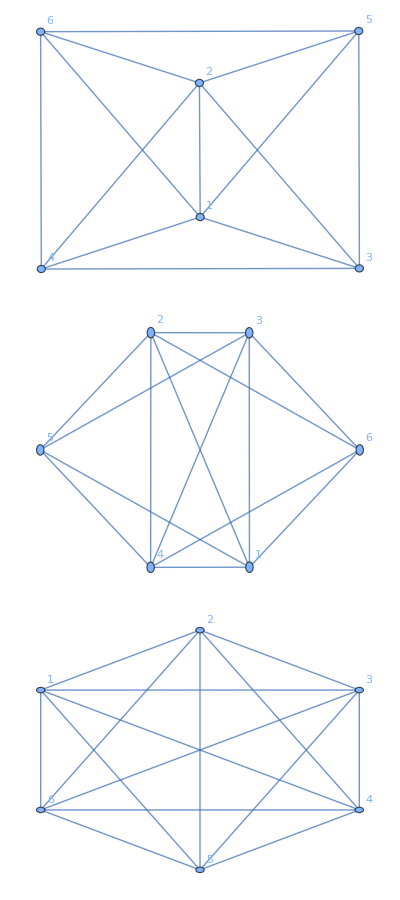

```mathematica
Column[Map[SetProperty[#, VertexLabels->Automatic]&, sixVGraphs[[-3;;]]]]
```

#### Entropy Vectors from the Adjacency Matrix

Next, we compute the entropy vector for every graph by feeding its adjacency matrix to ComputeEntropyVectorsAdj:

```mathematica
sixQGraphStatesSvecs = ComputeEntropyVectorsAdj[Map[AdjacencyMatrix, sixVGraphs]];
```

Because permutations of qubits yield equivalent entropy vectors, we identify vectors that are related by qubit exchange and keep a single representative of each symmetry orbit:

```mathematica
{baseVector, eqVectors}=EquivalentEntropyVectors[6];
sixQSvecsSymmetryOrbit=UniqueOrbits[sixQGraphStatesSvecs, baseVector, eqVectors]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1},{1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,1,1,1,1,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2},{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,2,2,1,1,2,2,1,2,2,2,2,0,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,1,1,1,2,2,1,1,2,2,1,2,2,2,2,1,1,1,2,2,1,2,2,2,2,1},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,2,2,1,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,1,1,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}}

Hence there are 26 distinct entropy vector symmetry orbits at six qubits.

#### Graph Representatives That Do Not Violate MMI

For each entropy‑vector orbit we would like a graph representative that does not violate the monogamy of mutual information (MMI) inequality.  The procedure is:

1. Enumerate all disjoint triples (i.e., every length-three list of pairwise disjoint system subsets) for six qubits.

```mathematica
sixQTriples=DisjointTriples[6];
```

2. Use MMIChecker to retain only those orbit representatives whose entropy vectors satisfy/saturate every MMI instance:

```mathematica
MMInonFailingSixQSvecs =Select[sixQSvecsSymmetryOrbit,( MMIChecker[#, sixQTriples]== True)&]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1},{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1},{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2},{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2},{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1},{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2},{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3},{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}}

3. Locate, inside sixVGraphs, the first graph that corresponds to a state that does not violate MMI:

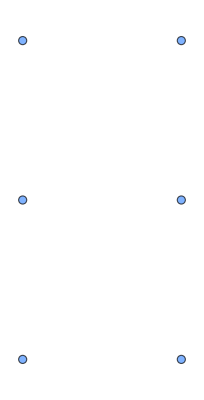
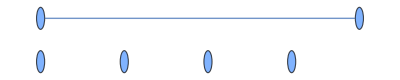
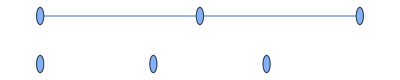
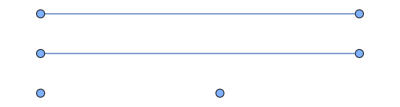
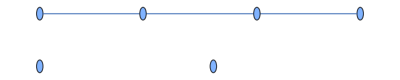
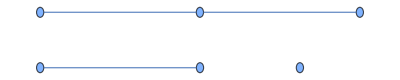
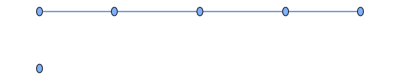
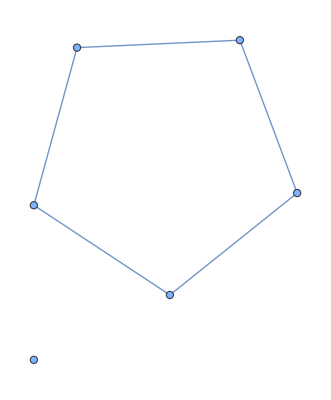

```mathematica
positionsMMInonFailingSixQSvecs =Flatten @Map[findFirstIndex[sixQGraphStatesSvecs, # ] &, Map[PermuteEntropyVector[#, baseVector, eqVectors ] &, MMInonFailingSixQSvecs]];
nonFailingGraphs=sixVGraphs[[positionsMMInonFailingSixQSvecs]]
```

We can associate each graph to the entropy vector of the graph state it represents:

```mathematica
nonFailingGraphInstance = AssociationThread[MMInonFailingSixQSvecs->nonFailingGraphs]
```

<|{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→-Graphics-,{1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1}→-Graphics-,{1,1,1,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,1,1,1,1,1,1,1}→-Graphics-,{1,1,1,1,0,0,0,2,2,1,1,2,2,1,1,0,1,1,1,1,0,1,1,0,0,1,2,2,2,2,1}→-Graphics-,{1,1,1,1,0,0,1,2,2,1,1,2,2,1,1,1,1,1,1,1,0,1,1,1,1,1,2,2,2,2,1}→-Graphics-,{1,1,1,1,1,0,1,1,2,2,1,1,2,2,1,2,2,1,0,1,1,0,2,2,1,2,2,1,1,2,2}→-Graphics-,{1,1,1,1,1,0,1,2,2,2,1,2,2,2,1,1,2,1,2,1,1,2,2,1,1,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,0,2,2,2,2,1,2,2,2,1,2,2,1,2,1,1,2,2,2,2,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,1,0,2,2,2,2,2,2,2,2,0,2,2,2,2,0,1,1,1,1,1,3,3,3,3,1}→-Graphics-,{1,1,1,1,1,1,1,1,2,2,2,1,2,2,2,2,2,2,1,1,1,0,2,2,2,2,2,2,2,2,2}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,0,1,1,2,2,1,3,3,3,3,1}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,1,2,2,2,2,2,3,3,3,3,2}→-Graphics-,{1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,1,2,2,3,3,3,3,2}→-Graphics-,{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,2,3,2,3,3}→-Graphics-,{1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3}→-Graphics-|>

#### LC-Equivalence of Graphs that Belong to non MMI-failing Graphs

Inspection shows that every connected graph in the non‑MMI‑failing set is locally complement (LC) equivalent to one of four graph families: sunlet, path, cycle, and wheel graphs. The single outlier,

, is LC‑equivalent to the six‑vertex wheel, as shown below:

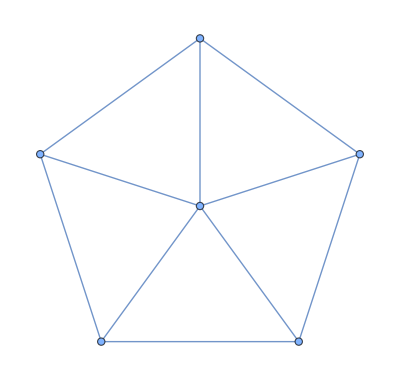
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@ -Graphics-]
```

True

### Graphs on Seven Vertices (Generation by Random Exploration)

#### Finding Non-MMI Failing Graph Representatives for Every Symmetry Orbit

Exhaustively listing the 2^(21) seven‑vertex simple undirected graphs is computationally heavy, yet we need only one graph per entropy‑vector orbit.  Fortunately, the number of symmetry orbits at n ≤ 12 is known (see arXiv:0504.4522). We exploit this fact:  a function generateSymmetryOrbitGraphRepresentatives samples random graphs until it has found a representative for each of the 59 orbits at seven qubits.  A typical call looks like

```mathematica
SeedRandom[314];
```

```mathematica
sevenVGraphSymmetryOrbits=generateSymmetryOrbitGraphRepresentatives[7,59];
```

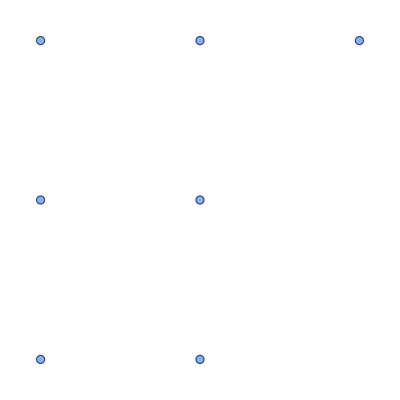
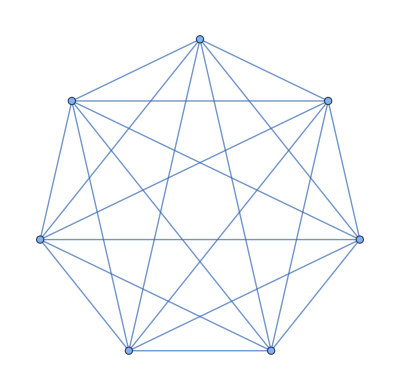
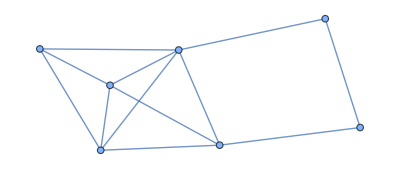
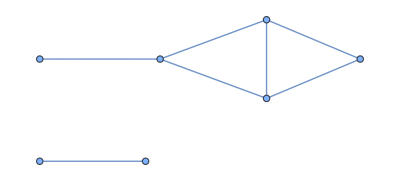
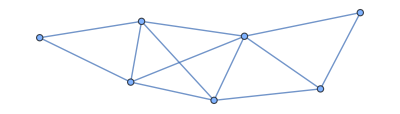
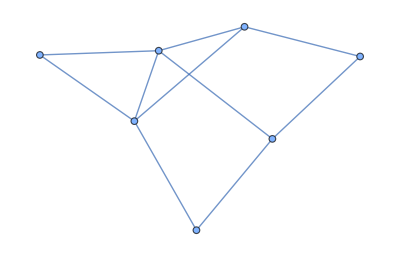
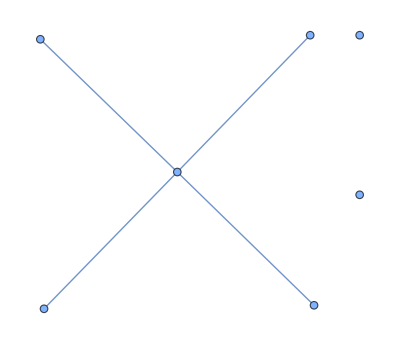
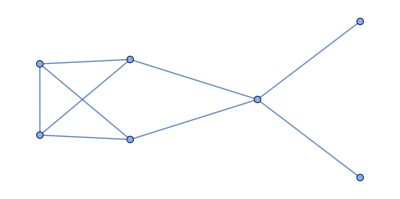

```mathematica
Map[AdjacencyGraph, sevenVGraphSymmetryOrbits]
```

#### Seven‑Qubit Graph States That Do Not Violate MMI

We again build the list of disjoint triples, test every candidate entropy vector with MMIChecker, and convert each remaining graph to a canonical form so its family is more evident:

```mathematica
sevenQTriples=DisjointTriples[7];
```

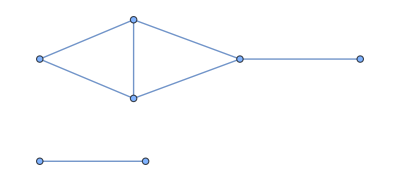
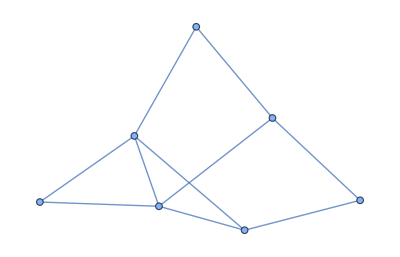
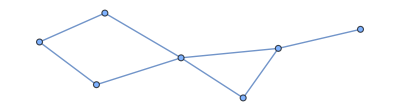
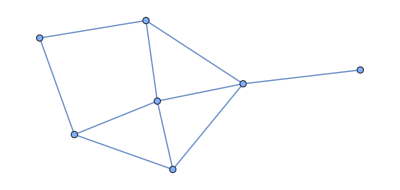
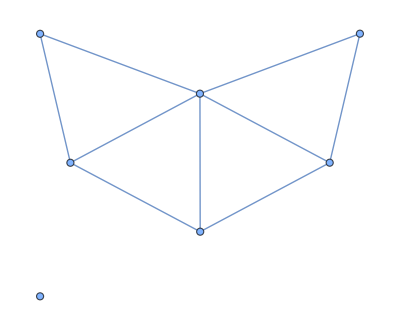
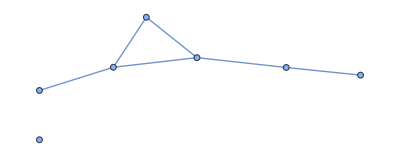
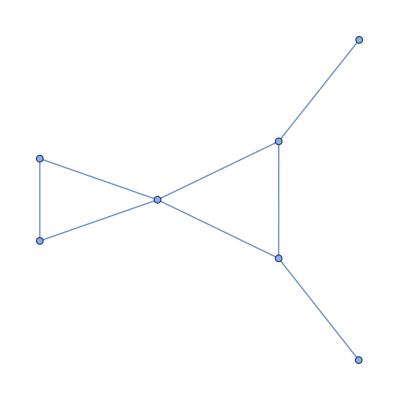
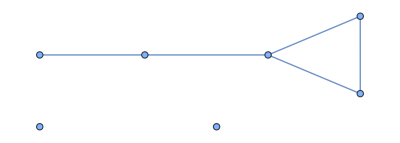
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MMInonFailingSevenGraphs =Select[sevenVGraphSymmetryOrbits, (MMIChecker[ComputeEntropyVectorsAdj[{#}][[1]], sevenQTriples]==True)&];
MMInonFailingSevenGraphs= Map[CanonicalGraph[AdjacencyGraph[#]]&, MMInonFailingSevenGraphs]
```

Connected graphs in MMInonFailingSevenGraphs interestingly, are exactly of a composition of path, cycle, sunlet, or wheel graphs:

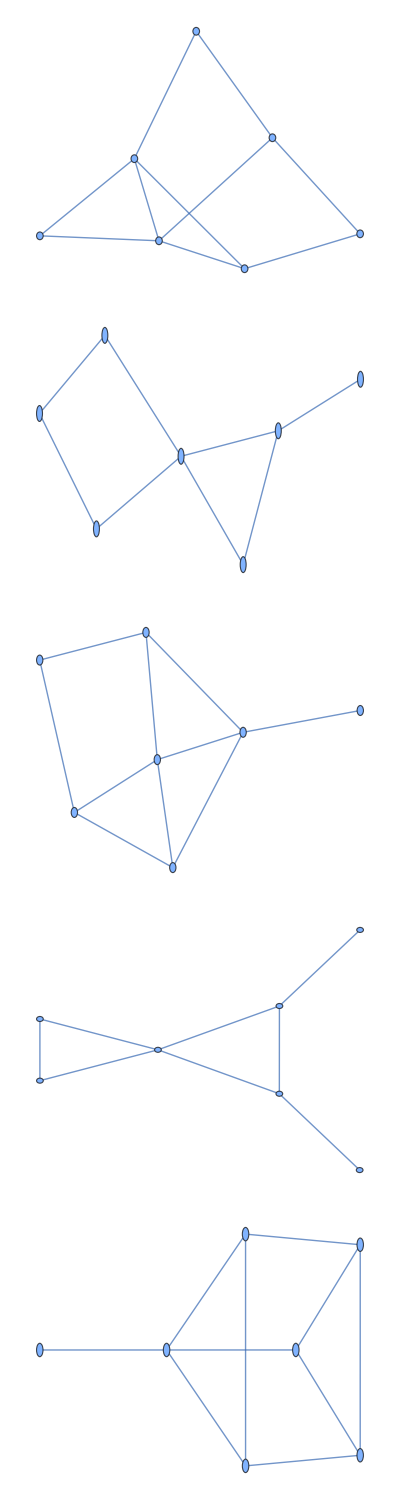

```mathematica
MMInonFailingSevenGraphsConnected=Select[MMInonFailingSevenGraphs, ConnectedGraphQ];
Column[MMInonFailingSevenGraphsConnected]
```

The second connected graph is LC equivalent to a path graph:

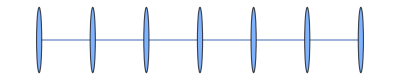
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@-Graphics-]
```

True

The first connected graph is LC equivalent to a cycle graph:

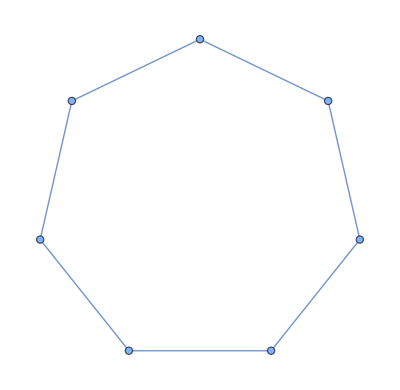
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

The fourth connected graph is a composition of a sunlet and a path graph.

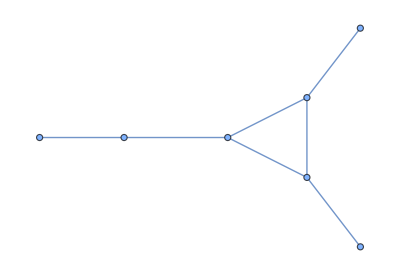
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

The third connected graph is LC equivalent to a composition of cycle graphs and a path graph :

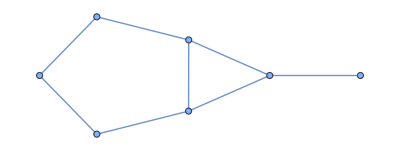
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-,AdjacencyMatrix@ -Graphics-]
```

True

Finally, the fifth  connected graph is LC equivalent to a composition of a wheel graph and a path graph:

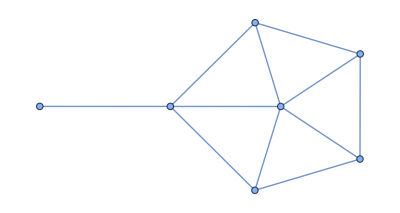
```mathematica
areLocalComplements[AdjacencyMatrix@-Graphics-, AdjacencyMatrix@-Graphics-]
```

True

Interestingly, the wheel graph on 7 vertices fails MMI:

```mathematica
MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@-Graphics-}][[1]], sevenQTriples]
```

False

However, it satisfies MMI again at 8 vertices:

False

```mathematica
MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@-Graphics-}][[1]], DisjointTriples[8]]
```

True

## Paper Results

## Section 4.4: Evidence of the Sufficiency of a Non-trivial Intersection for MMI Failure

The function allGeneralizedGraphsnoInnerNonTrivialInterInfo generates all generalized graphs from Section 4.3 (ignoring intra-region adjacencies) that exhibit at least one non-trivial intersection for some triple of the form {C, I, J}. Additionally, it provides the specific triples where such intersections occur.

We demonstrate exhaustively, up to n=8, that every such graph fails every MMI instance involving a non-trivial intersection. For n=9, we switch to a sampling-based approach using SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples, which randomly explores the space of Section 4.3-type adjacency matrices in search of graphs with at least one non-trivial intersection. While some connected graphs at n=9 do show saturation in certain MMI instances, we have not observed a single connected graph with a non-trivial intersection that satisfies its corresponding MMI instance.

### Data Gathering and Evaluation Procedure

For each n, we:
	1. Generate all graphs with at least one non-trivial intersection.
	2. Remove isomorphic duplicates.
	3. Use MMICheckerEntropyInput to evaluate each triple {C, I, J} that exhibits a non-trivial intersection.

### Generalized G Graphs With a Non-trivial Intersection

#### n=4

```mathematica
generalizedGraphFourVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[4];
generalizedGraphFourVInfo= DeleteDuplicates[generalizedGraphFourVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Only one unique graph remains:

```mathematica
generalizedGraphsFour=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphFourVInfo]
```

{-Graphics-}

MMI evaluations:

```mathematica
generalizedGraphsMMIEvaluationsFour=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphFourVInfo];
```

Notice how all such instances are failed:

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsFour ]
```

{True}

This same procedure is repeated for n = 5 through n = 8. In each case, every graph fails for all corresponding non-trivial intersection triples.

#### n = 5

```mathematica
generalizedGraphFiveVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[5];
generalizedGraphFiveVInfo= DeleteDuplicates[generalizedGraphFiveVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsFive=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphFiveVInfo]
```

{-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsFive=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphFiveVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsFive ]
```

{True,True,True}

#### n = 6

```mathematica
generalizedGraphSixVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[6];
generalizedGraphSixVInfo= DeleteDuplicates[generalizedGraphSixVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsSix=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphSixVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsSix=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphSixVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSix ]
```

{True,True,True,True,True,True,True,True,True,True,True}

#### n = 7

```mathematica
generalizedGraphSevenVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[7];
generalizedGraphSevenVInfo= DeleteDuplicates[generalizedGraphSevenVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsSeven=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphSevenVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsSeven=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphSevenVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSeven ]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### n = 8

```mathematica
generalizedGraphEightVInfo=allGeneralizedGraphsnoInnerNonTrivialInterInfo[8];
generalizedGraphEightVInfo= DeleteDuplicates[generalizedGraphEightVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

Graphs:

```mathematica
generalizedGraphsEight=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphEightVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs violate every MMI instance where a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsEight=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphEightVInfo];
```

```mathematica
Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsSeven ]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### n = 9: Sampling-Based Search

Due to computational limits, we use random sampling to generate graphs with potential non-trivial intersections:

```mathematica
SeedRandom[314159];
```

```mathematica
generalizedGraphNineVInfo=SampleAllGeneralizedGraphsnoInnerNonTrivialInterInfoTriples[9, 50];
generalizedGraphNineVInfo= DeleteDuplicates[generalizedGraphNineVInfo,(IsomorphicGraphQ[AdjacencyGraph@(#1[[1]]), AdjacencyGraph@(#2[[1]])])&];
```

The graphs we obtained by randomly sampling 50 of our generalized graphs for each center size are shown below:

```mathematica
generalizedGraphsNine=Map[AdjacencyGraph[#[[1]]]&, generalizedGraphNineVInfo]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Filtering for connected graphs:

```mathematica
generalizedGraphsNineConnectedInfo =Select[generalizedGraphNineVInfo,ConnectedGraphQ[AdjacencyGraph@#[[1]]]&];
generalizedGraphsNineConnected = Select[generalizedGraphsNine, ConnectedGraphQ]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Do all graphs above fail whenever a non-trivial intersection occurs?

```mathematica
generalizedGraphsMMIEvaluationsConnectedNine=Map[MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{#[[1]]}][[1]], #[[2]]]&, generalizedGraphsNineConnectedInfo];
```

```mathematica
fullyFailsIntNineQ=Map[AllTrue[#,#==="Fails"&]&,generalizedGraphsMMIEvaluationsConnectedNine ]
```

{True,True,True,True,True,False,True,False,True,False,True,False,False,True,True,True,False,True,True,True,True,False,True,False}

The pattern breaks! The following graphs saturate certain MMI instances where a non-trivial intersection occurs:

```mathematica
posNinenoFullFail=Flatten@Position[fullyFailsIntNineQ, False];
```

```mathematica
generalizedGraphsNineConnected[[posNinenoFullFail]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Among these connected graphs, only failure and saturation (not satisfaction) occurs:

```mathematica
Map[Select[#, (#!="Fails")&]&, generalizedGraphsMMIEvaluationsConnectedNine[[posNinenoFullFail]]]
```

{{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates},{Saturates,Saturates,Saturates,Saturates,Saturates,Saturates}}

To determine which triples are involved in the saturated instances:

```mathematica
triplesSaturateNineIndices=Map[(Flatten@(Position[#, "Saturates"]))&, generalizedGraphsMMIEvaluationsConnectedNine[[posNinenoFullFail]]]
```

{{28,29,36,37,39,40},{35,36,38,39,46,48},{25,26,27,28,29,30,31,32,34,35,37,38,40,41,43,45,47,49,51,53,55},{34,35,36,37,40,45},{25,26,28,29,31,32,34,35,36,37,38,39,40,41,43,45,47,49,50,51,52},{31,32,34,35,41,42},{28,29,36,37,45,46},{28,29,36,37,39,46}}

```mathematica
MapThread[Part,{generalizedGraphsNineConnectedInfo[[posNinenoFullFail]][[All,2]],triplesSaturateNineIndices}]
```

{{{{1,2,3},{4,7},{5,6}},{{1,2,3},{4,7},{8,9}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,6},{8,9}}},{{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{5,8},{6,7}},{{1,2,3},{5,9},{6,7}}},{{{1,2,3},{4,5},{6,7}},{{1,2,3},{4,5},{6,8}},{{1,2,3},{4,5},{6,9}},{{1,2,3},{4,5},{7,8}},{{1,2,3},{4,5},{7,9}},{{1,2,3},{4,5},{8,9}},{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,7},{5,8}},{{1,2,3},{4,7},{6,9}},{{1,2,3},{4,8},{5,7}},{{1,2,3},{4,8},{6,9}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,7},{6,9}},{{1,2,3},{5,8},{6,9}},{{1,2,3},{5,9},{7,8}},{{1,2,3},{6,7},{8,9}},{{1,2,3},{6,8},{7,9}},{{1,2,3},{6,9},{7,8}}},{{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{5,8},{6,7}}},{{{1,2,3},{4,5},{6,7}},{{1,2,3},{4,5},{8,9}},{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,7},{5,9}},{{1,2,3},{4,7},{6,8}},{{1,2,3},{4,8},{5,6}},{{1,2,3},{4,8},{5,7}},{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{4,8},{6,9}},{{1,2,3},{4,8},{7,9}},{{1,2,3},{4,9},{5,8}},{{1,2,3},{4,9},{6,7}},{{1,2,3},{5,6},{7,9}},{{1,2,3},{5,7},{6,9}},{{1,2,3},{5,8},{6,7}},{{1,2,3},{5,9},{6,7}},{{1,2,3},{5,9},{6,8}},{{1,2,3},{5,9},{7,8}},{{1,2,3},{6,7},{8,9}}},{{{1,2,3},{4,6},{5,8}},{{1,2,3},{4,6},{7,9}},{{1,2,3},{4,7},{5,8}},{{1,2,3},{4,7},{6,9}},{{1,2,3},{5,8},{6,9}},{{1,2,3},{5,8},{7,9}}},{{{1,2,3},{4,6},{5,9}},{{1,2,3},{4,6},{7,8}},{{1,2,3},{4,8},{5,9}},{{1,2,3},{4,8},{6,7}},{{1,2,3},{5,9},{6,7}},{{1,2,3},{5,9},{7,8}}},{{{1,2,3},{4,5},{6,9}},{{1,2,3},{4,5},{7,8}},{{1,2,3},{4,9},{5,6}},{{1,2,3},{4,9},{7,8}},{{1,2,3},{5,6},{7,8}},{{1,2,3},{6,9},{7,8}}}}

These outputs list the specific {C, I, J} triples corresponding to saturation. Despite this, no case of success has been observed for any triple in a connected graph with a non-trivial intersection.

## Section 4.4: Evidence of Non-MMI Failure for Different Families of Graphs

We now briefly examine the MMI failure status for three well-known families of graphs: path graphs, cycle graphs, and wheel graphs. Notably, up to  n=9, both path and cycle graphs consistently yield graph states that satisfy/saturate all MMI inequalities, none fail.

### Path Graphs

```mathematica
PnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@PathGraph[Range[n]]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{True,True,True,True,True,True}

### Cycle Graphs

```mathematica
CnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@CycleGraph[n]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{True,True,True,True,True,True}

### Wheel Graphs

In contrast, wheel graphs exhibit a more nuanced pattern. They fail  MMI at n=4, satisfy/saturate it for n=5 and n=6, fail again at n=7, and satisfy/saturate it once more for n=8 and n=9.

```mathematica
WnSatisfiesMMIQ =Flatten@Table[MMIChecker[ComputeEntropyVectorsAdj[{AdjacencyMatrix@WheelGraph[n]}][[1]], DisjointTriples[n]], {n,4,9}]
```

{False,True,True,False,True,True}

## Appendix A.3: Tables 10-12

```mathematica
SetDirectory["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8"]
```

C:\Users\Kaoti\OneDrive\Escritorio\Research\MMI Failure for Graph States\Data\MMI-Failure-Stars-n=8

```mathematica
Get["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8\\graphRepsSymmetryOrbitsEight.mx"]
```

Now, we present the procedure to replicate the data available in Tables 10-12 in the appendix A.3 in our paper.

First, we obtain graph representatives for each unique entropy vector at n=8.

```mathematica
graphRepsSymmetryOrbitsEight = generateSymmetryOrbitGraphRepresentatives[8, 182];
```

#### Generalized Star Representatives

```mathematica
LCOrbitsEight=ParallelMap[LCorbit,graphRepsSymmetryOrbitsEight];
```

```mathematica
centerEvaluationsLCOrbitsEight=findStarGraphReps[LCOrbitsEight, fourPartitions[8]];
```

```mathematica
StarLCorbitsEight=Module[{centers,evals,Greps},Table[
centers=orbit[[All,2]];
evals=Map[(#==="NF")&, centers];
Greps=Pick[orbit, evals, False ];
If[Greps!={}, Greps, "NF"]
,{orbit, centerEvaluationsLCOrbitsEight}]];
```

```mathematica
GeneralizedStarGraphsRepsEight=Map[First, StarLCorbitsEight];
```

```mathematica
MemberQ[GeneralizedStarGraphsRepsEight, "NF"]
```

False

```mathematica
nonGeneralizedStarGraphsEight=Module[{centers,evals,nonGreps},Flatten[Table[
centers=orbit[[All,2]];
evals=Map[(#==="NF")&, centers];
nonGreps=Pick[orbit, evals, True ];
If[nonGreps!={}, nonGreps, Nothing]
,{orbit, centerEvaluationsLCOrbitsEight}], 1]];
```

```mathematica
Length@nonGeneralizedStarGraphsEight
```

410

```mathematica
Length@Flatten[centerEvaluationsLCOrbitsEight, 1]
```

12346

```mathematica
DumpSave["LCOrbitsEight.mx", LCOrbitsEight];
DumpSave["centerEvaluationsLCOrbitsEight.mx", centerEvaluationsLCOrbitsEight];
DumpSave["StarLCorbitsEight.mx",StarLCorbitsEight];
DumpSave["GeneralizedStarGraphsRepsEight.mx", GeneralizedStarGraphsRepsEight];
DumpSave["nonGeneralizedStarGraphsEight.mx", nonGeneralizedStarGraphsEight];
```

#### Generalized Star Representatives (Graphs)

```mathematica
Map[AdjacencyGraph, GeneralizedStarGraphsRepsEight[[All,1]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Identify MMI Failing and Satisfying Cases

Now, we filter graph states in graphRepsSymmetryOrbitsEight according to whether they fail MMI or not:

```mathematica
uniqueEntropyVectorsEight=ComputeEntropyVectorsAdj[GeneralizedStarGraphsRepsEight[[All,1]]];
```

```mathematica
triplesEight=DisjointTriples[8];
```

```mathematica
DumpSave["uniqueEntropyVectorsEight.mx",uniqueEntropyVectorsEight];
DumpSave["triplesEight.mx",triplesEight];
```

```mathematica
Length@triplesEight
```

7770

```mathematica
evalsBool =ParallelMap[MMIChecker[#, triplesEight]&, uniqueEntropyVectorsEight];
```

```mathematica
starMMIFailLCorbisEight=Pick[StarLCorbitsEight, evalsBool, False];
starMMISatisfyLCorbisEight=Pick[StarLCorbitsEight, evalsBool, True];
```

```mathematica
DumpSave["starMMIFailLCorbisEight.mx",starMMIFailLCorbisEight];
DumpSave["starMMISatisfyLCorbisEight.mx",starMMISatisfyLCorbisEight];
```

```mathematica
nonTrivialColIntersections[starMFailCIJrep[[1,1]],{starMFailCIJrep[[1,2]]}]
```

{True,{{{4,5,6,7,8},{1},{2}}}}

#### Checking Nontrivial Intersections

```mathematica
ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts,"NF" ],{rep,orbit}]
,{orbit,starMMISatisfyLCorbisEight}]

ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts,"NF" ],{rep,orbit}]
,{orbit,starLCorbitsnoFailMMICIJwCenters}]
```

```mathematica
ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts[[1]],"NF" ],{rep,orbit}]
,{orbit,starLCorbitsFailMMICIJwCenters}]
```

```mathematica
ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
sVec=ComputeEntropyVectorsAdj[{rep[[1]]}][[1]];

failCIJ=Pick[CIJ,MMICheckerInputSelectTriples[sVec,CIJ], "Fails"];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], failCIJ];

Sort@failCIJ===Sort@nonTrivialInts[[2]],
 {rep,orbit}],
{orbit,starLCorbitsFailMMICIJwCenters}]
```

```mathematica
starLCorbitsFailMMICIJwCenters=Module[{adjRep, rep, CIJtriples, evals,orbitWfailCIreps},
ParallelTable[
orbitWfailCIreps=
Table[
adjRep=rep[[1]];
CIJtriples=Map[{#[[1]], #[[2,1]], #[[2,2]]}&,rep[[2]]];
evals=MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{adjRep}][[1]], CIJtriples];
If[MemberQ[evals, "Fails"], rep, Nothing],
{rep, orbit}];
If[orbitWfailCIreps==={}, Nothing, orbitWfailCIreps],
{orbit,starMMIFailLCorbisEight }]
];
```

```mathematica
starLCorbitsnoFailMMICIJwCenters=Module[{adjRep, rep, CIJtriples, evals,orbitWnofailCIreps},
ParallelTable[
orbitWnofailCIreps=
Table[
adjRep=rep[[1]];
CIJtriples=Map[{#[[1]], #[[2,1]], #[[2,2]]}&,rep[[2]]];
evals=MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{adjRep}][[1]], CIJtriples];
If[MemberQ[evals, "Fails"], Nothing, rep],
{rep, orbit}];
If[orbitWnofailCIreps===orbit, orbit, Nothing],
{orbit,starMMIFailLCorbisEight }]
];
```

#### Checking Nontrivial Intersections

```mathematica
ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts,"NF" ],{rep,orbit}]
,{orbit,starMMISatisfyLCorbisEight}];

ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts,"NF" ],{rep,orbit}]
,{orbit,starLCorbitsnoFailMMICIJwCenters}];
ParallelTable[
Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], CIJ];
If[nonTrivialInts[[1]],nonTrivialInts[[1]],"NF" ],{rep,orbit}]
,{orbit,starLCorbitsFailMMICIJwCenters}];
```

```mathematica
ParallelTable[Table[
allCIJK=rep[[2]];
CIJ=Map[{#[[1]], #[[2,1]], #[[2,2]]}&, allCIJK];
sVec=ComputeEntropyVectorsAdj[{rep[[1]]}][[1]];

failCIJ=Pick[CIJ,MMICheckerInputSelectTriples[sVec,CIJ], "Fails"];
nonTrivialInts=nonTrivialColIntersections[rep[[1]], failCIJ];

Sort@failCIJ===Sort@nonTrivialInts[[2]],
 {rep,orbit}],
{orbit,starLCorbitsFailMMICIJwCenters}]
```

```mathematica
DumpSave["starLCorbitsFailMMICIJwCenters.mx", starLCorbitsFailMMICIJwCenters];
DumpSave["starLCorbitsnoFailMMICIJwCenters.mx", starLCorbitsnoFailMMICIJwCenters];
```

#### Identifying a Relevant MMI Failed Instance

```mathematica
findMinimalEdgeRep[LCorbitsAndCenters_]:=Module[{adjs,evals},
ParallelTable[
adjs=orbit[[All,1]];
evals=Map[EdgeCount@AdjacencyGraph[#]&, adjs];
First@Pick[orbit, evals, Min[evals]],
{orbit,LCorbitsAndCenters }]
];
findBiggestCenter[repCenters_]:=Module[{centers,evals,CIJK},
centers=repCenters[[2]][[All,1]];
evals=Map[Length, centers];
CIJK=First@Pick[repCenters[[2]], evals, Max@evals];
{repCenters[[1]],{CIJK[[1]], CIJK[[2,1]],CIJK[[2,2]]}}
];
```

```mathematica
starMinimalEdgeSatisfyRep=findMinimalEdgeRep[starMMISatisfyLCorbisEight];
starMinimalEdgeFailCIJRep=findMinimalEdgeRep[starLCorbitsFailMMICIJwCenters];
starminimalEdgeFailOtherRep=findMinimalEdgeRep[starLCorbitsnoFailMMICIJwCenters];
```

```mathematica
DumpSave["starMinimalEdgeSatisfyRep.mx", starMinimalEdgeSatisfyRep];
DumpSave["starMinimalEdgeFailCIJRep.mx", starMinimalEdgeFailCIJRep];
DumpSave["starminimalEdgeFailOtherRep.mx", starminimalEdgeFailOtherRep];
```

```mathematica
starMBigCenterSatisfyRep=Map[findBiggestCenter, starMinimalEdgeSatisfyRep];
starmMBigCenterFailOtherRep=Map[findBiggestCenter, starminimalEdgeFailOtherRep];
```

```mathematica
DumpSave["starMBigCenterSatisfyRep.mx", starMBigCenterSatisfyRep];
DumpSave["starmMBigCenterFailOtherRep.mx", starmMBigCenterFailOtherRep];
```

```mathematica
Get["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8\\triplesEight.mx"];
```

```mathematica
starMFailCIJrep=Module[{CIJtriples,evalsCIJ, centersFail, centerFailLenghts, CIJK},
ParallelTable[
CIJtriples=rep[[2]][[All,2]];
evalsCIJ=MMICheckerInputSelectTriples[ComputeEntropyVectorsAdj[{rep[[1]]}][[1]], CIJtriples];
centersFail= Pick[rep[[2]], evalsCIJ, "Fails"];
centerFailLenghts=Map[Length[#[[1]]]&,centersFail];
CIJK=First@Pick[centersFail, centerFailLenghts, Max@centerFailLenghts];
{rep[[1]],{CIJK[[1]], CIJK[[2,1]], CIJK[[2,2]]}},
{rep,starMinimalEdgeFailCIJRep}]
];
```

```mathematica
starMFailOtherMMIwCenter=Module[{sVecs, evals, repFailedTriples, failedTriplesLength},
sVecs=ComputeEntropyVectorsAdj[starmMBigCenterFailOtherRep[[All,1]]];
evals =ParallelMap[MMICheckerInputSelectTriples[#, triplesEight]&,sVecs];

ParallelTable[
repFailedTriples=Pick[triplesEight, evals[[i]], "Fails"];
failedTriplesLength=Map[Length@Join[#[[1]], #[[2]],#[[3]]]&,repFailedTriples ];
{starmMBigCenterFailOtherRep[[i,1]], First@Pick[repFailedTriples, failedTriplesLength, Max@failedTriplesLength], starmMBigCenterFailOtherRep[[i,2]]}
,{i, Length@starmMBigCenterFailOtherRep}]
];
```

```mathematica
DumpSave["starMBigCenterSatisfyRep.mx", starMBigCenterSatisfyRep];
DumpSave["starMFailCIJrep.mx", starMFailCIJrep];
DumpSave["starMFailOtherMMIwCenter.mx", starMFailOtherMMIwCenter];
```

For those that fail, identify largest failing instance of type (C,I,J) for those that showcase a nontrivial intersection, and simply largest instance for those that do not .

Finally, we compute MMI evaluation count and organize from least to greatest satisfy/fail count , giving the actual ordering seen in the tables.

```mathematica
(*Length of longest simple path per component=diameter*)
componentDiameters[adj_]:=Module[{G},G=AdjacencyGraph[Unitize@adj,DirectedEdges->False];
GraphDiameter/@(Subgraph[G,#]&/@ConnectedComponents[G])];

(*Tie-break tuple:{max,#max,secondMax,#secondMax}*)
pathTieBreaker[adj_]:=Module[{diams=componentDiameters[adj],maxD,cntMax,secondD,cntSecond},If[diams==={},Return[{0,0,0,0}]];
maxD=Max[diams];
cntMax=Count[diams,maxD];
secondD=If[Length[DeleteDuplicates[diams]]>=2,Max@DeleteCases[diams,maxD],0];
cntSecond=Count[diams,secondD];
{maxD,cntMax,secondD,cntSecond}];
```

```mathematica
satisfySvecs=ComputeEntropyVectorsAdj[starMBigCenterSatisfyRep[[All,1]]];
evalsSatisfy=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, satisfySvecs];
evalsSatisfyCount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsSatisfy];
minimalStarSatisfyMMICount=Join[starMBigCenterSatisfyRep,evalsSatisfyCount,2 ];
starRepsSatisfyMMICount=SortBy[minimalStarSatisfyMMICount,{#[[3,1]]&,Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];
starRepsSatisfyMMICount=Map[{#[[1]], {}, #[[2]], #[[3]]}&, starRepsSatisfyMMICount];
```

```mathematica
FailsCIJSvecs=ComputeEntropyVectorsAdj[starMFailCIJrep[[All,1]]];
evalsFailsCIJ=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, FailsCIJSvecs];
evalsFailsCIJcount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsFailsCIJ];
minimalStarFailCIJCount=Join[starMFailCIJrep,evalsFailsCIJcount,2 ];
minimalStarFailCIJCount=SortBy[minimalStarFailCIJCount,{#[[3,3]]&, Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];
```

```mathematica
FailsnoCIJSvecs=ComputeEntropyVectorsAdj[starMFailOtherMMIwCenter[[All,1]]];
evalsFailsnoCIJ=ParallelMap[
MMICheckerInputSelectTriples[#, triplesEight]&, FailsnoCIJSvecs];
evalsFailsnoCIJcount=ParallelMap[{{Count[#,"Satisfies"], Count[#,"Saturates"],Count[#,"Fails"]}}&, evalsFailsnoCIJ];
minimalStarFailOtherMMI=Join[starMFailOtherMMIwCenter,evalsFailsnoCIJcount,2 ];
minimalStarFailOtherMMI=SortBy[minimalStarFailOtherMMI,{#[[4,3]]&, Total@Flatten@#[[1]]&,pathTieBreaker[#[[1]]]&}];
```

```mathematica
DumpSave["starRepsSatisfyMMICount.mx", starRepsSatisfyMMICount];
DumpSave["minimalStarFailCIJCount.mx", minimalStarFailCIJCount];
DumpSave["minimalStarFailOtherMMI.mx", minimalStarFailOtherMMI];
```

```mathematica
minimalStarFailOtherMMI[[1]]
```

{SparseArray[…],{{1,6},{2,5},{3,4}},{{3,4,6,7,8},{1},{2}},{4920,2846,4}}

#### Tables 10-12 Construction

```mathematica
minimalStarFailCIJCount[[2]]
```

{SparseArray[…],{{5,7,8},{3},{4}},{4848,2918,4}}

```mathematica
starRepsSatisfyMMICount[[1]]
```

{SparseArray[…],{{1,5,6,7,8},{2},{3}},{0,7770,0}}

```mathematica
Get["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8\\minimalStarFailCIJCount.mx"];
Get["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8\\minimalStarFailOtherMMI.mx"];
```

```mathematica
Subsets[Range[5], {4}]
```

{{1,2,3,4},{1,2,3,5},{1,2,4,5},{1,3,4,5},{2,3,4,5}}

```mathematica
hasFourStar[adj_]:=Module[{graph=AdjacencyGraph@adj, vertices=Range[Length@adj], fourStar=StarGraph[4], fourSubsets, evals},
fourSubsets=Subsets[vertices, {4}];
evals =Map[IsomorphicGraphQ[Subgraph[graph, #], fourStar]&, fourSubsets];
MemberQ[evals,True]
]
```

```mathematica
ParallelMap[hasFourStar, minimalStarFailCIJCount[[All,1]]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ParallelMap[hasFourStar, minimalStarFailOtherMMI[[All,1]]]
```

{True,True,True,True,True,True,True,True}

```mathematica
g1Tab14=AdjacencyGraph[#, VertexLabels->Automatic]&@minimalStarFailOtherMMI[[1,1]]
```

-Graphics-

```mathematica
gWithStar=LocalComplementation[AdjacencyMatrix@g1Tab14, 7]
```

SparseArray[…]

```mathematica
SetDirectory["C:\\Users\\Kaoti\\OneDrive\\Escritorio\\Research\\MMI Failure for Graph States\\Data\\MMI-Failure-Stars-n=8"]
```

C:\Users\Kaoti\OneDrive\Escritorio\Research\MMI Failure for Graph States\Data\MMI-Failure-Stars-n=8

```mathematica
DumpSave["minimalStarFailOtherMMI.mx", minimalStarFailOtherMMI]
```

{{{SparseArray[…],{{1,6},{2,5},{3,4}},{{3,4,6,7,8},{1},{2}},{4920,2846,4}},{SparseArray[…],{{1,5},{2,6},{3,4}},{{4,5,6,7,8},{1},{2}},{4728,3038,4}},{SparseArray[…],{{1,2},{3,5},{4,8}},{{2,4,5,6,7},{1},{3}},{5096,2662,12}},{SparseArray[…],{{2,5},{3,6},{1,4,7}},{{4,5,6,7,8},{1},{2}},{4496,3258,16}},{SparseArray[…],{{1,5},{2,6},{3,4,8}},{{4,5,6,7,8},{1},{2}},{5244,2510,16}},{SparseArray[…],{{2,3},{6,7},{1,5,8}},{{4,5,6,7,8},{1},{2}},{4608,3134,28}},{SparseArray[…],{{1,2},{3,4},{5,6}},{{2,3,4,7,8},{1},{5}},{4088,3654,28}},{SparseArray[…],{{2,3},{5,6},{1,7,8}},{{4,5,6,7,8},{1},{2}},{3696,3962,112}}}}

```mathematica
minimalStarFailOtherMMI[[1,1]]=gWithStar
```

SparseArray[…]

```mathematica
EdgeCount[gWithStar]
```

14

```mathematica
hasFourStar[gWithStar]
```

True

```mathematica
hasFourStar[AdjacencyMatrix@CompleteGraph[6]]
```

False

```mathematica
TikZTableFromAdjTriples[starRepsSatisfyMMICount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
```

```mathematica
Length@Bipartitions[10][[All,1]]
```

511

```mathematica
TikZTableFromAdjTriples[minimalStarFailCIJCount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
```

```mathematica
TikZTableFromAdjTriples[minimalStarFailOtherMMI,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"ABC"]
```

\begin{longtable}{>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}>{\centering\arraybackslash}m{\dimexpr\linewidth/6-2\tabcolsep\relax}}
\endfirsthead
\endhead
\endfoot
\endlastfoot
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4920,2846,4)};
\node[Anode,BorderTriangle] (v1) at (3.290,1.751) {\scriptsize 1};
\node[Bnode,BorderSquare] (v2) at (1.230,1.184) {\scriptsize 2};
\node[CnodeABC,BorderStar] (v3) at (1.230,2.316) {\scriptsize 3};
\node[CnodeABC,BorderStar] (v4) at (0.210,1.304) {\scriptsize 4};
\node[Bnode] (v5) at (0.210,2.197) {\scriptsize 5};
\node[Anode,BorderStar] (v6) at (2.193,1.750) {\scriptsize 6};
\node[Knode,BorderStar] (v7) at (1.556,1.750) {\scriptsize 7};
\node[Knode,BorderStar] (v8) at (0.743,1.751) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (1)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4728,3038,4)};
\node[Anode,BorderTriangle] (v1) at (0.684,0.682) {\scriptsize 1};
\node[Bnode,BorderSquare] (v2) at (3.290,1.320) {\scriptsize 2};
\node[CnodeABC] (v3) at (1.489,2.022) {\scriptsize 3};
\node[CnodeABC,BorderStar] (v4) at (1.446,2.998) {\scriptsize 4};
\node[Anode,BorderStar] (v5) at (0.210,2.143) {\scriptsize 5};
\node[Bnode,BorderStar] (v6) at (2.793,2.761) {\scriptsize 6};
\node[Knode,BorderStar] (v7) at (2.052,0.502) {\scriptsize 7};
\node[Knode,BorderStar] (v8) at (1.997,1.357) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (2)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5096,2662,12)};
\node[Anode,BorderTriangle] (v1) at (3.290,2.183) {\scriptsize 1};
\node[Anode,BorderStar] (v2) at (3.289,1.317) {\scriptsize 2};
\node[Bnode,BorderSquare] (v3) at (0.210,1.318) {\scriptsize 3};
\node[CnodeABC,BorderStar] (v4) at (0.212,2.183) {\scriptsize 4};
\node[Bnode,BorderStar] (v5) at (1.322,1.333) {\scriptsize 5};
\node[Knode,BorderStar] (v6) at (2.178,2.166) {\scriptsize 6};
\node[Knode,BorderStar] (v7) at (2.176,1.332) {\scriptsize 7};
\node[CnodeABC] (v8) at (1.323,2.167) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v4);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (3)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4496,3258,16)};
\node[CnodeABC,BorderTriangle] (v1) at (3.290,3.005) {\scriptsize 1};
\node[Anode,BorderSquare] (v2) at (0.715,3.005) {\scriptsize 2};
\node[Bnode] (v3) at (1.333,1.748) {\scriptsize 3};
\node[CnodeABC,BorderStar] (v4) at (0.708,0.495) {\scriptsize 4};
\node[Anode,BorderStar] (v5) at (2.046,2.501) {\scriptsize 5};
\node[Bnode,BorderStar] (v6) at (2.669,1.745) {\scriptsize 6};
\node[CnodeABC,BorderStar] (v7) at (2.042,0.993) {\scriptsize 7};
\node[Knode,BorderStar] (v8) at (0.210,1.752) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v8);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v6) -- (v7);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (4)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (5244,2510,16)};
\node[Anode,BorderTriangle] (v1) at (0.241,0.210) {\scriptsize 1};
\node[Bnode,BorderSquare] (v2) at (3.290,0.242) {\scriptsize 2};
\node[CnodeABC] (v3) at (0.210,3.258) {\scriptsize 3};
\node[CnodeABC,BorderStar] (v4) at (3.257,3.290) {\scriptsize 4};
\node[Anode,BorderStar] (v5) at (0.692,1.740) {\scriptsize 5};
\node[Bnode,BorderStar] (v6) at (2.806,1.761) {\scriptsize 6};
\node[Knode,BorderStar] (v7) at (1.761,0.693) {\scriptsize 7};
\node[CnodeABC,BorderStar] (v8) at (1.738,2.807) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v5);
\draw[line width=0.9pt,line cap=round] (v1) -- (v7);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (5)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4608,3134,28)};
\node[CnodeABC,BorderTriangle] (v1) at (3.290,2.062) {\scriptsize 1};
\node[Anode,BorderSquare] (v2) at (0.210,2.522) {\scriptsize 2};
\node[Anode] (v3) at (2.168,2.683) {\scriptsize 3};
\node[Knode,BorderStar] (v4) at (1.237,0.605) {\scriptsize 4};
\node[CnodeABC,BorderStar] (v5) at (1.225,2.895) {\scriptsize 5};
\node[Bnode,BorderStar] (v6) at (0.776,1.563) {\scriptsize 6};
\node[Bnode,BorderStar] (v7) at (2.071,1.341) {\scriptsize 7};
\node[CnodeABC,BorderStar] (v8) at (1.937,2.025) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v8);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (6)}
\vspace{5pt}
\end{minipage} \\
\begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (4088,3654,28)};
\node[Anode,BorderTriangle] (v1) at (1.368,1.749) {\scriptsize 1};
\node[Anode,BorderStar] (v2) at (2.387,0.608) {\scriptsize 2};
\node[Bnode,BorderStar] (v3) at (0.210,1.749) {\scriptsize 3};
\node[Bnode,BorderStar] (v4) at (2.385,2.893) {\scriptsize 4};
\node[CnodeABC,BorderSquare] (v5) at (1.116,0.607) {\scriptsize 5};
\node[CnodeABC] (v6) at (3.290,1.752) {\scriptsize 6};
\node[Knode,BorderStar] (v7) at (1.114,2.892) {\scriptsize 7};
\node[Knode,BorderStar] (v8) at (2.133,1.750) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v1) -- (v2);
\draw[line width=0.9pt,line cap=round] (v1) -- (v3);
\draw[line width=0.9pt,line cap=round] (v1) -- (v4);
\draw[line width=0.9pt,line cap=round] (v2) -- (v5);
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v5);
\draw[line width=0.9pt,line cap=round] (v3) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v6);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\draw[line width=0.9pt,line cap=round] (v6) -- (v8);
\draw[line width=0.9pt,line cap=round] (v7) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (7)}
\vspace{5pt}
\end{minipage} & \begin{minipage}[t]{\linewidth}\centering
\vspace{5pt}
\resizebox{0.960\linewidth}{!}{\begin{tikzpicture}[scale=1]
\path[use as bounding box] (-0.100,-0.100) rectangle (3.600,3.780);
\node[anchor=south, inner sep=0pt] at (1.750,3.680) {\large (3696,3962,112)};
\node[CnodeABC,BorderTriangle] (v1) at (0.500,0.210) {\scriptsize 1};
\node[Anode,BorderSquare] (v2) at (1.149,0.830) {\scriptsize 2};
\node[Anode] (v3) at (0.591,3.290) {\scriptsize 3};
\node[Knode,BorderStar] (v4) at (3.000,2.543) {\scriptsize 4};
\node[Bnode,BorderStar] (v5) at (1.580,2.221) {\scriptsize 5};
\node[Bnode,BorderStar] (v6) at (0.500,1.976) {\scriptsize 6};
\node[CnodeABC,BorderStar] (v7) at (2.333,1.407) {\scriptsize 7};
\node[CnodeABC,BorderStar] (v8) at (1.908,3.280) {\scriptsize 8};
\begin{scope}[on background layer]
\draw[line width=0.9pt,line cap=round] (v2) -- (v6);
\draw[line width=0.9pt,line cap=round] (v2) -- (v7);
\draw[line width=0.9pt,line cap=round] (v3) -- (v6);
\draw[line width=0.9pt,line cap=round] (v3) -- (v8);
\draw[line width=0.9pt,line cap=round] (v4) -- (v7);
\draw[line width=0.9pt,line cap=round] (v4) -- (v8);
\draw[line width=0.9pt,line cap=round] (v5) -- (v6);
\draw[line width=0.9pt,line cap=round] (v5) -- (v7);
\draw[line width=0.9pt,line cap=round] (v5) -- (v8);
\end{scope}
\end{tikzpicture}}\\[4pt]
{\small\bfseries (8)}
\vspace{5pt}
\end{minipage} &   &   &   &   \\
\end{longtable}

Finally, we call TikZTableFromAdjTriples to directly generate Table 10 - 12

```mathematica
Print["Table 11"];
TikZTableFromAdjTriples[starRepsSatisfyMMICount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
Print["Table 12"];
TikZTableFromAdjTriples[minimalStarNonTFailCIJCount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"CIJ"]
Print["Table 13"];
TikZTableFromAdjTriples[minimalStarTFailnoCIJCount,Columns->6,RowVspace->"5pt",MultiPage->True,Version->"Color",CanvasCM->3.5,(*per-graph square canvas (cm)*)PanelNumbering->True,(*show (1),(2),…*)PanelStyle->"\\small\\bfseries" (*bigger panel numbers*), EvalLabelSize->"\\large",EvalLabelOffsetCM->{0,0.18}, ColorScheme->"ABC"]
```